# CrSBr double layer magnon dispersion with applied magnetic field

To calculate the dipolar magnon dispersion, we express the magnetization of each sublattice as the summation of the equilibrium magnetization and dynamic magnetization.
That is,

We aim to solve the Landau-Lifshitz equation 



for the magnon dispersion.

```mathematica
Clear[gamma,Ms,J,Kx,Kz,Hz,Theta,hx,hy,hz,kx,ky,kz];
```

```mathematica
Clear[gamma,Ms,J,Kx,Kz,Hz,Theta,hx,hy,hz,kx,ky,kz];
M1={Ms*Cos[Theta]-ma*Sin[Theta],m1y,Ms*Sin[Theta]+ma*Cos[Theta]};
m1x = M1[[1]];
m1z = M1[[3]];
M2={-Ms*Cos[Theta]-mb*Sin[Theta],m2y,Ms*Sin[Theta]-mb*Cos[Theta]};
m2x = M2[[1]];
m2z = M2[[3]];
```

For the first sublattice, the equilibrium magnetization is along the direction (cos(θ), 0, sin(θ)), so the two axes for the dynamic magnetization are (-sin(θ), 0, cos(θ)) (m_a direction) and (0, 1, 0) (m_(1y) direction). For the second sublattice, the equilibrium magnetization is along the direction (-cos(θ), 0, sin(θ)), so the two axes for the dynamic magnetization are (-sin(θ), 0, -cos(θ)) (m_b direction) and (0, 1, 0) (m_(2y) direction). The effective field H_i^eff is calculated below.

```mathematica
H1 = {(2*Kx*m1x)/Ms^2-(J*m2x)/Ms^2+hx,(-J*m2y)/Ms^2+hy,(-2*Kz*m1z)/Ms^2-(J*m2z)/Ms^2+Hz+hz};
H2 = {(2*Kx*m2x)/Ms^2-(J*m1x)/Ms^2+hx,(-J*m1y)/Ms^2+hy,(-2*Kz*m2z)/Ms^2-(J*m1z)/Ms^2+Hz+hz};
```

Then we calculate the cross-product term ). We start with the cross product term along the m_(1y) direction for the first sublattice.

```mathematica
CrossM1=FullSimplify[Cross[M1,H1]];
CrossM1[[2]]
```

(hx ma-(hz+Hz) Ms) Cos[Theta]+(((J+2 (Kx+Kz)) ma-J mb) Cos[2 Theta])/Ms+(hz+Hz) ma Sin[Theta]+hx Ms Sin[Theta]+(J+Kx+Kz) Sin[2 Theta]+(ma (-((Kx+Kz) ma)+J mb) Sin[2 Theta])/Ms^2

We ignore second order terms in  and  (since they are assumed to be small?)

```mathematica
Cross1y = (-(hz+Hz) Ms) Cos[Theta]+(((J+2 (Kx+Kz)) ma-J mb) Cos[2 Theta])/Ms+(Hz) ma Sin[Theta]+hx Ms Sin[Theta]+(J+Kx+Kz) Sin[2 Theta]
```

(-hz-Hz) Ms Cos[Theta]+(((J+2 (Kx+Kz)) ma-J mb) Cos[2 Theta])/Ms+Hz ma Sin[Theta]+hx Ms Sin[Theta]+(J+Kx+Kz) Sin[2 Theta]

Then we also get the cross product along the  direction for sublattice 1 via

```mathematica
Cross1a = FullSimplify[CrossM1.{-Sin[Theta],0,Cos[Theta]}]
```

1/Ms^2(Ms (-Kx m1y+Kz m1y-J m2y+hy Ms^2)+m1y (-hx Ms^2 Cos[Theta]-(J+Kx+Kz) Ms Cos[2 Theta]-(hz+Hz) Ms^2 Sin[Theta]+((Kx+Kz) ma-J mb) Sin[2 Theta]))

And again we only keep first order terms in the m and h

```mathematica
Cross1a = FullSimplify[1/Ms^2(Ms (-Kx m1y+Kz m1y-J m2y+hy Ms^2)+m1y (-(J+Kx+Kz) Ms Cos[2 Theta]-(Hz) Ms^2 Sin[Theta]))]
```

-(Kx m1y-Kz m1y+J m2y-hy Ms^2+(J+Kx+Kz) m1y Cos[2 Theta]+Hz m1y Ms Sin[Theta])/Ms

Now we repeat for the second sublattice, only calculating the cross product along the  direction

```mathematica
CrossM2=FullSimplify[Cross[M2,H2]];
CrossM2[[2]]
```

(-hx mb+(hz+Hz) Ms) Cos[Theta]+((-J ma+(J+2 (Kx+Kz)) mb) Cos[2 Theta])/Ms+((hz+Hz) mb+hx Ms) Sin[Theta]-(J+Kx+Kz) Sin[2 Theta]+(mb (-J ma+(Kx+Kz) mb) Sin[2 Theta])/Ms^2

```mathematica
Cross2y = ((hz+Hz) Ms) Cos[Theta]+((-J ma+(J+2 (Kx+Kz)) mb) Cos[2 Theta])/Ms+((Hz) mb+hx Ms) Sin[Theta]-(J+Kx+Kz) Sin[2 Theta];
Cross2b = FullSimplify[CrossM2.{-Sin[Theta],0,-Cos[Theta]}]
```

1/Ms^2(Ms (-J m1y-Kx m2y+Kz m2y+hy Ms^2)+m2y (hx Ms^2 Cos[Theta]-(J+Kx+Kz) Ms Cos[2 Theta]-(hz+Hz) Ms^2 Sin[Theta]+(J ma-(Kx+Kz) mb) Sin[2 Theta]))

```mathematica
Cross2b = FullSimplify[1/Ms^2(Ms (-J m1y-Kx m2y+Kz m2y+hy Ms^2)+m2y (-(J+Kx+Kz) Ms Cos[2 Theta]-(Hz) Ms^2 Sin[Theta]))];
```

Now for the angle , which determines the direction of equilibrium magnetization, there are two cases:

      if       
                               if      

where  is the saturation magnetic field 
Case 1 is below

```mathematica
Hs = 2(J+Kx+Kz)/Ms;
If[Hz>Hs, Print[Text[Warning! Hz > Hs so case one does not apply]]];
```

```mathematica
Theta =ArcSin[Hz/Hs]
```

ArcSin[(Hz Ms)/(2 (J+Kx+Kz))]

```mathematica
Cross1a=FullSimplify[Cross1a]
Cross1y =FullSimplify[ Cross1y]
Cross2b = FullSimplify[Cross2b]
Cross2y=FullSimplify[Cross2y]
```

(-2 Kx m1y-J (m1y+m2y)+hy Ms^2)/Ms

1/2 Ms ((Hz (Hz ma+hx Ms))/(J+Kx+Kz)-hz √(4-(Hz^2 Ms^2)/(J+Kx+Kz)^2))+1/Ms(2 (Kx+Kz) ma+J (ma-mb)) Cos[2 ArcSin[(Hz Ms)/(2 (J+Kx+Kz))]]

(-2 Kx m2y-J (m1y+m2y)+hy Ms^2)/Ms

1/2 Ms ((Hz (Hz mb+hx Ms))/(J+Kx+Kz)+hz √(4-(Hz^2 Ms^2)/(J+Kx+Kz)^2))+1/Ms(2 (Kx+Kz) mb+J (-ma+mb)) Cos[2 ArcSin[(Hz Ms)/(2 (J+Kx+Kz))]]

Note that cos(2arcsin(x)) = 1-2x^2. So we can simplify Cross1y and Cross2y

```mathematica
Cross1y = FullSimplify[1/2 Ms ((Hz (Hz ma+hx Ms))/(J+Kx+Kz)-hz √(4-(Hz^2 Ms^2)/(J+Kx+Kz)^2))+((2 (Kx+Kz) ma+J (ma-mb)) (1-2 ((Hz Ms)/(2 (J+Kx+Kz)))^2))/Ms]
Cross2y = FullSimplify[1/2 Ms ((Hz (Hz mb+hx Ms))/(J+Kx+Kz)+hz √(4-(Hz^2 Ms^2)/(J+Kx+Kz)^2))+((2 (Kx+Kz) mb+J (-ma+mb))(1-2 ((Hz Ms)/(2 (J+Kx+Kz)))^2))/Ms]
```

((2 (Kx+Kz) ma+J (ma-mb)) (1-(Hz^2 Ms^2)/(2 (J+Kx+Kz)^2)))/Ms+1/2 Ms ((Hz (Hz ma+hx Ms))/(J+Kx+Kz)-hz √(4-(Hz^2 Ms^2)/(J+Kx+Kz)^2))

((2 (Kx+Kz) mb+J (-ma+mb)) (1-(Hz^2 Ms^2)/(2 (J+Kx+Kz)^2)))/Ms+1/2 Ms ((Hz (Hz mb+hx Ms))/(J+Kx+Kz)+hz √(4-(Hz^2 Ms^2)/(J+Kx+Kz)^2))

Now solving the LL equation and assuming the m’s and h’s have the form of plane waves, we can express 
in terms of

```mathematica
Clear[omega];
sol1=FullSimplify[Solve[I*omega*m1y==gamma*Cross1y && I*omega*ma==gamma*Cross1a && I*omega*m2y==gamma*Cross2y && I*omega*mb==gamma*Cross2b ,{m1y,ma,m2y,mb}]];
M1y=FullSimplify[(m1y/.sol1)][[1]]
Ma=FullSimplify[(ma/.sol1)][[1]]
M2y=FullSimplify[(m2y/.sol1)][[1]]
Mb=FullSimplify[(mb/.sol1)][[1]]
```

(gamma Ms^2 (-gamma^3 hy Kx (16 (Kx+Kz) (J+Kx+Kz)^4+4 Hz^2 (J+Kx+Kz)^2 (J-2 (Kx+Kz)) Ms^2+Hz^4 (-J+Kx+Kz) Ms^4)+ⅈ gamma^2 (J+Kx+Kz) Ms (hx Hz Kx Ms (-4 (J+Kx+Kz)^2+Hz^2 Ms^2)+hz (J+Kx) (4 (Kx+Kz) (J+Kx+Kz)^2-Hz^2 (-J+Kx+Kz) Ms^2) √(4-(Hz^2 Ms^2)/(J+Kx+Kz)^2)) omega+gamma hy (J+Kx+Kz) Ms^2 (4 (Kx+Kz) (J+Kx+Kz)^2-Hz^2 (-J+Kx+Kz) Ms^2) omega^2+ⅈ (J+Kx+Kz)^2 Ms^3 (hx Hz Ms-hz (J+Kx+Kz) √(4-(Hz^2 Ms^2)/(J+Kx+Kz)^2)) omega^3))/(2 (-gamma^4 Kx (J+Kx) (16 (Kx+Kz) (J+Kx+Kz)^4+4 Hz^2 (J+Kx+Kz)^2 (J-2 (Kx+Kz)) Ms^2+Hz^4 (-J+Kx+Kz) Ms^4)+gamma^2 (J+Kx+Kz) Ms^2 (4 (J+Kx+Kz)^2 (2 Kx (Kx+Kz)+J (2 Kx+Kz))+Hz^2 (J^2-J (Kx+Kz)-2 Kx (Kx+Kz)) Ms^2) omega^2-(J+Kx+Kz)^3 Ms^4 omega^4))

-((gamma (J+Kx+Kz) Ms^2 (gamma^3 Kx (J+Kx) (-4 hx Hz (J+Kx+Kz)^2 Ms+hx Hz^3 Ms^3+hz (4 (Kx+Kz) (J+Kx+Kz)^2-Hz^2 (-J+Kx+Kz) Ms^2) √(4-(Hz^2 Ms^2)/(J+Kx+Kz)^2))+ⅈ gamma^2 hy Kx (J+Kx+Kz) Ms (2 (J+Kx+Kz)-Hz Ms) (2 (J+Kx+Kz)+Hz Ms) omega-gamma (J+Kx+Kz) Ms^2 (-hx Hz (J+Kx) Ms+hz Kx (J+Kx+Kz) √(4-(Hz^2 Ms^2)/(J+Kx+Kz)^2)) omega^2-ⅈ hy (J+Kx+Kz)^2 Ms^3 omega^3))/(-gamma^4 Kx (J+Kx) (16 (Kx+Kz) (J+Kx+Kz)^4+4 Hz^2 (J+Kx+Kz)^2 (J-2 (Kx+Kz)) Ms^2+Hz^4 (-J+Kx+Kz) Ms^4)+gamma^2 (J+Kx+Kz) Ms^2 (4 (J+Kx+Kz)^2 (2 Kx (Kx+Kz)+J (2 Kx+Kz))+Hz^2 (J^2-J (Kx+Kz)-2 Kx (Kx+Kz)) Ms^2) omega^2-(J+Kx+Kz)^3 Ms^4 omega^4))

(gamma Ms^2 (gamma^3 hy Kx (16 (Kx+Kz) (J+Kx+Kz)^4+4 Hz^2 (J+Kx+Kz)^2 (J-2 (Kx+Kz)) Ms^2+Hz^4 (-J+Kx+Kz) Ms^4)+ⅈ gamma^2 (J+Kx+Kz) Ms (hx Hz Kx Ms (4 (J+Kx+Kz)^2-Hz^2 Ms^2)+hz (J+Kx) (4 (Kx+Kz) (J+Kx+Kz)^2-Hz^2 (-J+Kx+Kz) Ms^2) √(4-(Hz^2 Ms^2)/(J+Kx+Kz)^2)) omega-gamma hy (J+Kx+Kz) Ms^2 (4 (Kx+Kz) (J+Kx+Kz)^2-Hz^2 (-J+Kx+Kz) Ms^2) omega^2-ⅈ (J+Kx+Kz)^2 Ms^3 (hx Hz Ms+hz (J+Kx+Kz) √(4-(Hz^2 Ms^2)/(J+Kx+Kz)^2)) omega^3))/(2 (gamma^4 Kx (J+Kx) (16 (Kx+Kz) (J+Kx+Kz)^4+4 Hz^2 (J+Kx+Kz)^2 (J-2 (Kx+Kz)) Ms^2+Hz^4 (-J+Kx+Kz) Ms^4)-gamma^2 (J+Kx+Kz) Ms^2 (4 (J+Kx+Kz)^2 (2 Kx (Kx+Kz)+J (2 Kx+Kz))+Hz^2 (J^2-J (Kx+Kz)-2 Kx (Kx+Kz)) Ms^2) omega^2+(J+Kx+Kz)^3 Ms^4 omega^4))

-((gamma (J+Kx+Kz) Ms^2 (-gamma^3 Kx (J+Kx) (4 hx Hz (J+Kx+Kz)^2 Ms-hx Hz^3 Ms^3+hz (4 (Kx+Kz) (J+Kx+Kz)^2-Hz^2 (-J+Kx+Kz) Ms^2) √(4-(Hz^2 Ms^2)/(J+Kx+Kz)^2))+ⅈ gamma^2 hy Kx (J+Kx+Kz) Ms (2 (J+Kx+Kz)-Hz Ms) (2 (J+Kx+Kz)+Hz Ms) omega+gamma (J+Kx+Kz) Ms^2 (hx Hz (J+Kx) Ms+hz Kx (J+Kx+Kz) √(4-(Hz^2 Ms^2)/(J+Kx+Kz)^2)) omega^2-ⅈ hy (J+Kx+Kz)^2 Ms^3 omega^3))/(-gamma^4 Kx (J+Kx) (16 (Kx+Kz) (J+Kx+Kz)^4+4 Hz^2 (J+Kx+Kz)^2 (J-2 (Kx+Kz)) Ms^2+Hz^4 (-J+Kx+Kz) Ms^4)+gamma^2 (J+Kx+Kz) Ms^2 (4 (J+Kx+Kz)^2 (2 Kx (Kx+Kz)+J (2 Kx+Kz))+Hz^2 (J^2-J (Kx+Kz)-2 Kx (Kx+Kz)) Ms^2) omega^2-(J+Kx+Kz)^3 Ms^4 omega^4))

We change coordinates for net dynamic magnetization to xyz from aby

```mathematica
Mx = FullSimplify[-Ma*Sin[Theta]-Mb*Sin[Theta]]
My = FullSimplify[M1y+M2y]
Mz = FullSimplify[Ma*Cos[Theta]-Mb*Cos[Theta]]
```

(gamma Hz Ms^4 (gamma hx Hz (J+Kx)-ⅈ hy (J+Kx+Kz) omega))/(gamma^2 (J+Kx) (4 (Kx+Kz) (J+Kx+Kz)^2-Hz^2 (-J+Kx+Kz) Ms^2)-(J+Kx+Kz)^2 Ms^2 omega^2)

(gamma Ms^2 (gamma hy (4 (Kx+Kz) (J+Kx+Kz)^2-Hz^2 (-J+Kx+Kz) Ms^2)+ⅈ hx Hz (J+Kx+Kz) Ms^2 omega))/(gamma^2 (J+Kx) (4 (Kx+Kz) (J+Kx+Kz)^2-Hz^2 (-J+Kx+Kz) Ms^2)-(J+Kx+Kz)^2 Ms^2 omega^2)

(gamma^2 hz Kx Ms^2 (4 (J+Kx+Kz)^2-Hz^2 Ms^2))/((J+Kx+Kz) (gamma^2 Kx (4 (J+Kx+Kz)^2-Hz^2 Ms^2)-(J+Kx+Kz) Ms^2 omega^2))

Next we calculate  and use the Maxwell equation  to solve for the magnon dispersion

```mathematica
{bx, by, bz} = {hx + 4Pi*Mx, hy + 4 Pi*My, hz + 4 Pi*Mz}
```

{hx+(4 gamma Hz Ms^4 (gamma hx Hz (J+Kx)-ⅈ hy (J+Kx+Kz) omega) π)/(gamma^2 (J+Kx) (4 (Kx+Kz) (J+Kx+Kz)^2-Hz^2 (-J+Kx+Kz) Ms^2)-(J+Kx+Kz)^2 Ms^2 omega^2),hy+(4 gamma Ms^2 (gamma hy (4 (Kx+Kz) (J+Kx+Kz)^2-Hz^2 (-J+Kx+Kz) Ms^2)+ⅈ hx Hz (J+Kx+Kz) Ms^2 omega) π)/(gamma^2 (J+Kx) (4 (Kx+Kz) (J+Kx+Kz)^2-Hz^2 (-J+Kx+Kz) Ms^2)-(J+Kx+Kz)^2 Ms^2 omega^2),hz+(4 gamma^2 hz Kx Ms^2 (4 (J+Kx+Kz)^2-Hz^2 Ms^2) π)/((J+Kx+Kz) (gamma^2 Kx (4 (J+Kx+Kz)^2-Hz^2 Ms^2)-(J+Kx+Kz) Ms^2 omega^2))}

```mathematica
Clear[kx,ky,kz,J,Kx,Kz,gamma,Ms,Hz];
dispersion1=Solve[Coefficient[bx,hx]*kx^2+Coefficient[by,hy]*ky^2+Coefficient[bz,hz]*kz^2==0,{omega}];
omegaSol1 = omega/.dispersion1;
omegaLow1 = omegaSol1[[2]]
omegaHigh1 = omegaSol1[[4]]
```

(√(8 gamma^2 J^5 kx^2 Kx Ms^2+40 gamma^2 J^4 kx^2 Kx^2 Ms^2+80 gamma^2 J^3 kx^2 Kx^3 Ms^2+80 gamma^2 J^2 kx^2 Kx^4 Ms^2+40 gamma^2 J kx^2 Kx^5 Ms^2+8 gamma^2 kx^2 Kx^6 Ms^2+8 gamma^2 J^5 Kx ky^2 Ms^2+40 gamma^2 J^4 Kx^2 ky^2 Ms^2+80 gamma^2 J^3 Kx^3 ky^2 Ms^2+80 gamma^2 J^2 Kx^4 ky^2 Ms^2+40 gamma^2 J Kx^5 ky^2 Ms^2+8 gamma^2 Kx^6 ky^2 Ms^2+8 gamma^2 J^5 Kx kz^2 Ms^2+40 gamma^2 J^4 Kx^2 kz^2 Ms^2+80 gamma^2 J^3 Kx^3 kz^2 Ms^2+80 gamma^2 J^2 Kx^4 kz^2 Ms^2+40 gamma^2 J Kx^5 kz^2 Ms^2+8 gamma^2 Kx^6 kz^2 Ms^2+4 gamma^2 J^5 kx^2 Kz Ms^2+56 gamma^2 J^4 kx^2 Kx Kz Ms^2+184 gamma^2 J^3 kx^2 Kx^2 Kz Ms^2+256 gamma^2 J^2 kx^2 Kx^3 Kz Ms^2+164 gamma^2 J kx^2 Kx^4 Kz Ms^2+40 gamma^2 kx^2 Kx^5 Kz Ms^2+4 gamma^2 J^5 ky^2 Kz Ms^2+56 gamma^2 J^4 Kx ky^2 Kz Ms^2+184 gamma^2 J^3 Kx^2 ky^2 Kz Ms^2+256 gamma^2 J^2 Kx^3 ky^2 Kz Ms^2+164 gamma^2 J Kx^4 ky^2 Kz Ms^2+40 gamma^2 Kx^5 ky^2 Kz Ms^2+4 gamma^2 J^5 kz^2 Kz Ms^2+56 gamma^2 J^4 Kx kz^2 Kz Ms^2+184 gamma^2 J^3 Kx^2 kz^2 Kz Ms^2+256 gamma^2 J^2 Kx^3 kz^2 Kz Ms^2+164 gamma^2 J Kx^4 kz^2 Kz Ms^2+40 gamma^2 Kx^5 kz^2 Kz Ms^2+16 gamma^2 J^4 kx^2 Kz^2 Ms^2+128 gamma^2 J^3 kx^2 Kx Kz^2 Ms^2+288 gamma^2 J^2 kx^2 Kx^2 Kz^2 Ms^2+256 gamma^2 J kx^2 Kx^3 Kz^2 Ms^2+80 gamma^2 kx^2 Kx^4 Kz^2 Ms^2+16 gamma^2 J^4 ky^2 Kz^2 Ms^2+128 gamma^2 J^3 Kx ky^2 Kz^2 Ms^2+288 gamma^2 J^2 Kx^2 ky^2 Kz^2 Ms^2+256 gamma^2 J Kx^3 ky^2 Kz^2 Ms^2+80 gamma^2 Kx^4 ky^2 Kz^2 Ms^2+16 gamma^2 J^4 kz^2 Kz^2 Ms^2+128 gamma^2 J^3 Kx kz^2 Kz^2 Ms^2+288 gamma^2 J^2 Kx^2 kz^2 Kz^2 Ms^2+256 gamma^2 J Kx^3 kz^2 Kz^2 Ms^2+80 gamma^2 Kx^4 kz^2 Kz^2 Ms^2+24 gamma^2 J^3 kx^2 Kz^3 Ms^2+128 gamma^2 J^2 kx^2 Kx Kz^3 Ms^2+184 gamma^2 J kx^2 Kx^2 Kz^3 Ms^2+80 gamma^2 kx^2 Kx^3 Kz^3 Ms^2+24 gamma^2 J^3 ky^2 Kz^3 Ms^2+128 gamma^2 J^2 Kx ky^2 Kz^3 Ms^2+184 gamma^2 J Kx^2 ky^2 Kz^3 Ms^2+80 gamma^2 Kx^3 ky^2 Kz^3 Ms^2+24 gamma^2 J^3 kz^2 Kz^3 Ms^2+128 gamma^2 J^2 Kx kz^2 Kz^3 Ms^2+184 gamma^2 J Kx^2 kz^2 Kz^3 Ms^2+80 gamma^2 Kx^3 kz^2 Kz^3 Ms^2+16 gamma^2 J^2 kx^2 Kz^4 Ms^2+56 gamma^2 J kx^2 Kx Kz^4 Ms^2+40 gamma^2 kx^2 Kx^2 Kz^4 Ms^2+16 gamma^2 J^2 ky^2 Kz^4 Ms^2+56 gamma^2 J Kx ky^2 Kz^4 Ms^2+40 gamma^2 Kx^2 ky^2 Kz^4 Ms^2+16 gamma^2 J^2 kz^2 Kz^4 Ms^2+56 gamma^2 J Kx kz^2 Kz^4 Ms^2+40 gamma^2 Kx^2 kz^2 Kz^4 Ms^2+4 gamma^2 J kx^2 Kz^5 Ms^2+8 gamma^2 kx^2 Kx Kz^5 Ms^2+4 gamma^2 J ky^2 Kz^5 Ms^2+8 gamma^2 Kx ky^2 Kz^5 Ms^2+4 gamma^2 J kz^2 Kz^5 Ms^2+8 gamma^2 Kx kz^2 Kz^5 Ms^2+gamma^2 Hz^2 J^4 kx^2 Ms^4+gamma^2 Hz^2 J^3 kx^2 Kx Ms^4-3 gamma^2 Hz^2 J^2 kx^2 Kx^2 Ms^4-5 gamma^2 Hz^2 J kx^2 Kx^3 Ms^4-2 gamma^2 Hz^2 kx^2 Kx^4 Ms^4+gamma^2 Hz^2 J^4 ky^2 Ms^4+gamma^2 Hz^2 J^3 Kx ky^2 Ms^4-3 gamma^2 Hz^2 J^2 Kx^2 ky^2 Ms^4-5 gamma^2 Hz^2 J Kx^3 ky^2 Ms^4-2 gamma^2 Hz^2 Kx^4 ky^2 Ms^4+gamma^2 Hz^2 J^4 kz^2 Ms^4+gamma^2 Hz^2 J^3 Kx kz^2 Ms^4-3 gamma^2 Hz^2 J^2 Kx^2 kz^2 Ms^4-5 gamma^2 Hz^2 J Kx^3 kz^2 Ms^4-2 gamma^2 Hz^2 Kx^4 kz^2 Ms^4+gamma^2 Hz^2 J^3 kx^2 Kz Ms^4-4 gamma^2 Hz^2 J^2 kx^2 Kx Kz Ms^4-11 gamma^2 Hz^2 J kx^2 Kx^2 Kz Ms^4-6 gamma^2 Hz^2 kx^2 Kx^3 Kz Ms^4+gamma^2 Hz^2 J^3 ky^2 Kz Ms^4-4 gamma^2 Hz^2 J^2 Kx ky^2 Kz Ms^4-11 gamma^2 Hz^2 J Kx^2 ky^2 Kz Ms^4-6 gamma^2 Hz^2 Kx^3 ky^2 Kz Ms^4+gamma^2 Hz^2 J^3 kz^2 Kz Ms^4-4 gamma^2 Hz^2 J^2 Kx kz^2 Kz Ms^4-11 gamma^2 Hz^2 J Kx^2 kz^2 Kz Ms^4-6 gamma^2 Hz^2 Kx^3 kz^2 Kz Ms^4-gamma^2 Hz^2 J^2 kx^2 Kz^2 Ms^4-7 gamma^2 Hz^2 J kx^2 Kx Kz^2 Ms^4-6 gamma^2 Hz^2 kx^2 Kx^2 Kz^2 Ms^4-gamma^2 Hz^2 J^2 ky^2 Kz^2 Ms^4-7 gamma^2 Hz^2 J Kx ky^2 Kz^2 Ms^4-6 gamma^2 Hz^2 Kx^2 ky^2 Kz^2 Ms^4-gamma^2 Hz^2 J^2 kz^2 Kz^2 Ms^4-7 gamma^2 Hz^2 J Kx kz^2 Kz^2 Ms^4-6 gamma^2 Hz^2 Kx^2 kz^2 Kz^2 Ms^4-gamma^2 Hz^2 J kx^2 Kz^3 Ms^4-2 gamma^2 Hz^2 kx^2 Kx Kz^3 Ms^4-gamma^2 Hz^2 J ky^2 Kz^3 Ms^4-2 gamma^2 Hz^2 Kx ky^2 Kz^3 Ms^4-gamma^2 Hz^2 J kz^2 Kz^3 Ms^4-2 gamma^2 Hz^2 Kx kz^2 Kz^3 Ms^4+16 gamma^2 J^4 Kx ky^2 Ms^4 π+64 gamma^2 J^3 Kx^2 ky^2 Ms^4 π+96 gamma^2 J^2 Kx^3 ky^2 Ms^4 π+64 gamma^2 J Kx^4 ky^2 Ms^4 π+16 gamma^2 Kx^5 ky^2 Ms^4 π+16 gamma^2 J^4 Kx kz^2 Ms^4 π+64 gamma^2 J^3 Kx^2 kz^2 Ms^4 π+96 gamma^2 J^2 Kx^3 kz^2 Ms^4 π+64 gamma^2 J Kx^4 kz^2 Ms^4 π+16 gamma^2 Kx^5 kz^2 Ms^4 π+16 gamma^2 J^4 ky^2 Kz Ms^4 π+128 gamma^2 J^3 Kx ky^2 Kz Ms^4 π+288 gamma^2 J^2 Kx^2 ky^2 Kz Ms^4 π+256 gamma^2 J Kx^3 ky^2 Kz Ms^4 π+80 gamma^2 Kx^4 ky^2 Kz Ms^4 π+64 gamma^2 J^3 Kx kz^2 Kz Ms^4 π+192 gamma^2 J^2 Kx^2 kz^2 Kz Ms^4 π+192 gamma^2 J Kx^3 kz^2 Kz Ms^4 π+64 gamma^2 Kx^4 kz^2 Kz Ms^4 π+64 gamma^2 J^3 ky^2 Kz^2 Ms^4 π+288 gamma^2 J^2 Kx ky^2 Kz^2 Ms^4 π+384 gamma^2 J Kx^2 ky^2 Kz^2 Ms^4 π+160 gamma^2 Kx^3 ky^2 Kz^2 Ms^4 π+96 gamma^2 J^2 Kx kz^2 Kz^2 Ms^4 π+192 gamma^2 J Kx^2 kz^2 Kz^2 Ms^4 π+96 gamma^2 Kx^3 kz^2 Kz^2 Ms^4 π+96 gamma^2 J^2 ky^2 Kz^3 Ms^4 π+256 gamma^2 J Kx ky^2 Kz^3 Ms^4 π+160 gamma^2 Kx^2 ky^2 Kz^3 Ms^4 π+64 gamma^2 J Kx kz^2 Kz^3 Ms^4 π+64 gamma^2 Kx^2 kz^2 Kz^3 Ms^4 π+64 gamma^2 J ky^2 Kz^4 Ms^4 π+80 gamma^2 Kx ky^2 Kz^4 Ms^4 π+16 gamma^2 Kx kz^2 Kz^4 Ms^4 π+16 gamma^2 ky^2 Kz^5 Ms^4 π+4 gamma^2 Hz^2 J^3 kx^2 Ms^6 π+12 gamma^2 Hz^2 J^2 kx^2 Kx Ms^6 π+12 gamma^2 Hz^2 J kx^2 Kx^2 Ms^6 π+4 gamma^2 Hz^2 kx^2 Kx^3 Ms^6 π+4 gamma^2 Hz^2 J^3 ky^2 Ms^6 π+4 gamma^2 Hz^2 J^2 Kx ky^2 Ms^6 π-4 gamma^2 Hz^2 J Kx^2 ky^2 Ms^6 π-4 gamma^2 Hz^2 Kx^3 ky^2 Ms^6 π-4 gamma^2 Hz^2 J^2 Kx kz^2 Ms^6 π-8 gamma^2 Hz^2 J Kx^2 kz^2 Ms^6 π-4 gamma^2 Hz^2 Kx^3 kz^2 Ms^6 π+8 gamma^2 Hz^2 J^2 kx^2 Kz Ms^6 π+16 gamma^2 Hz^2 J kx^2 Kx Kz Ms^6 π+8 gamma^2 Hz^2 kx^2 Kx^2 Kz Ms^6 π+4 gamma^2 Hz^2 J^2 ky^2 Kz Ms^6 π-8 gamma^2 Hz^2 J Kx ky^2 Kz Ms^6 π-12 gamma^2 Hz^2 Kx^2 ky^2 Kz Ms^6 π-8 gamma^2 Hz^2 J Kx kz^2 Kz Ms^6 π-8 gamma^2 Hz^2 Kx^2 kz^2 Kz Ms^6 π+4 gamma^2 Hz^2 J kx^2 Kz^2 Ms^6 π+4 gamma^2 Hz^2 kx^2 Kx Kz^2 Ms^6 π-4 gamma^2 Hz^2 J ky^2 Kz^2 Ms^6 π-12 gamma^2 Hz^2 Kx ky^2 Kz^2 Ms^6 π-4 gamma^2 Hz^2 Kx kz^2 Kz^2 Ms^6 π-4 gamma^2 Hz^2 ky^2 Kz^3 Ms^6 π-√(-4 (J^4 kx^2 Ms^4+4 J^3 kx^2 Kx Ms^4+6 J^2 kx^2 Kx^2 Ms^4+4 J kx^2 Kx^3 Ms^4+kx^2 Kx^4 Ms^4+J^4 ky^2 Ms^4+4 J^3 Kx ky^2 Ms^4+6 J^2 Kx^2 ky^2 Ms^4+4 J Kx^3 ky^2 Ms^4+Kx^4 ky^2 Ms^4+J^4 kz^2 Ms^4+4 J^3 Kx kz^2 Ms^4+6 J^2 Kx^2 kz^2 Ms^4+4 J Kx^3 kz^2 Ms^4+Kx^4 kz^2 Ms^4+4 J^3 kx^2 Kz Ms^4+12 J^2 kx^2 Kx Kz Ms^4+12 J kx^2 Kx^2 Kz Ms^4+4 kx^2 Kx^3 Kz Ms^4+4 J^3 ky^2 Kz Ms^4+12 J^2 Kx ky^2 Kz Ms^4+12 J Kx^2 ky^2 Kz Ms^4+4 Kx^3 ky^2 Kz Ms^4+4 J^3 kz^2 Kz Ms^4+12 J^2 Kx kz^2 Kz Ms^4+12 J Kx^2 kz^2 Kz Ms^4+4 Kx^3 kz^2 Kz Ms^4+6 J^2 kx^2 Kz^2 Ms^4+12 J kx^2 Kx Kz^2 Ms^4+6 kx^2 Kx^2 Kz^2 Ms^4+6 J^2 ky^2 Kz^2 Ms^4+12 J Kx ky^2 Kz^2 Ms^4+6 Kx^2 ky^2 Kz^2 Ms^4+6 J^2 kz^2 Kz^2 Ms^4+12 J Kx kz^2 Kz^2 Ms^4+6 Kx^2 kz^2 Kz^2 Ms^4+4 J kx^2 Kz^3 Ms^4+4 kx^2 Kx Kz^3 Ms^4+4 J ky^2 Kz^3 Ms^4+4 Kx ky^2 Kz^3 Ms^4+4 J kz^2 Kz^3 Ms^4+4 Kx kz^2 Kz^3 Ms^4+kx^2 Kz^4 Ms^4+ky^2 Kz^4 Ms^4+kz^2 Kz^4 Ms^4) (16 gamma^4 J^6 kx^2 Kx^2+96 gamma^4 J^5 kx^2 Kx^3+240 gamma^4 J^4 kx^2 Kx^4+320 gamma^4 J^3 kx^2 Kx^5+240 gamma^4 J^2 kx^2 Kx^6+96 gamma^4 J kx^2 Kx^7+16 gamma^4 kx^2 Kx^8+16 gamma^4 J^6 Kx^2 ky^2+96 gamma^4 J^5 Kx^3 ky^2+240 gamma^4 J^4 Kx^4 ky^2+320 gamma^4 J^3 Kx^5 ky^2+240 gamma^4 J^2 Kx^6 ky^2+96 gamma^4 J Kx^7 ky^2+16 gamma^4 Kx^8 ky^2+16 gamma^4 J^6 Kx^2 kz^2+96 gamma^4 J^5 Kx^3 kz^2+240 gamma^4 J^4 Kx^4 kz^2+320 gamma^4 J^3 Kx^5 kz^2+240 gamma^4 J^2 Kx^6 kz^2+96 gamma^4 J Kx^7 kz^2+16 gamma^4 Kx^8 kz^2+16 gamma^4 J^6 kx^2 Kx Kz+176 gamma^4 J^5 kx^2 Kx^2 Kz+640 gamma^4 J^4 kx^2 Kx^3 Kz+1120 gamma^4 J^3 kx^2 Kx^4 Kz+1040 gamma^4 J^2 kx^2 Kx^5 Kz+496 gamma^4 J kx^2 Kx^6 Kz+96 gamma^4 kx^2 Kx^7 Kz+16 gamma^4 J^6 Kx ky^2 Kz+176 gamma^4 J^5 Kx^2 ky^2 Kz+640 gamma^4 J^4 Kx^3 ky^2 Kz+1120 gamma^4 J^3 Kx^4 ky^2 Kz+1040 gamma^4 J^2 Kx^5 ky^2 Kz+496 gamma^4 J Kx^6 ky^2 Kz+96 gamma^4 Kx^7 ky^2 Kz+16 gamma^4 J^6 Kx kz^2 Kz+176 gamma^4 J^5 Kx^2 kz^2 Kz+640 gamma^4 J^4 Kx^3 kz^2 Kz+1120 gamma^4 J^3 Kx^4 kz^2 Kz+1040 gamma^4 J^2 Kx^5 kz^2 Kz+496 gamma^4 J Kx^6 kz^2 Kz+96 gamma^4 Kx^7 kz^2 Kz+80 gamma^4 J^5 kx^2 Kx Kz^2+560 gamma^4 J^4 kx^2 Kx^2 Kz^2+1440 gamma^4 J^3 kx^2 Kx^3 Kz^2+1760 gamma^4 J^2 kx^2 Kx^4 Kz^2+1040 gamma^4 J kx^2 Kx^5 Kz^2+240 gamma^4 kx^2 Kx^6 Kz^2+80 gamma^4 J^5 Kx ky^2 Kz^2+560 gamma^4 J^4 Kx^2 ky^2 Kz^2+1440 gamma^4 J^3 Kx^3 ky^2 Kz^2+1760 gamma^4 J^2 Kx^4 ky^2 Kz^2+1040 gamma^4 J Kx^5 ky^2 Kz^2+240 gamma^4 Kx^6 ky^2 Kz^2+80 gamma^4 J^5 Kx kz^2 Kz^2+560 gamma^4 J^4 Kx^2 kz^2 Kz^2+1440 gamma^4 J^3 Kx^3 kz^2 Kz^2+1760 gamma^4 J^2 Kx^4 kz^2 Kz^2+1040 gamma^4 J Kx^5 kz^2 Kz^2+240 gamma^4 Kx^6 kz^2 Kz^2+160 gamma^4 J^4 kx^2 Kx Kz^3+800 gamma^4 J^3 kx^2 Kx^2 Kz^3+1440 gamma^4 J^2 kx^2 Kx^3 Kz^3+1120 gamma^4 J kx^2 Kx^4 Kz^3+320 gamma^4 kx^2 Kx^5 Kz^3+160 gamma^4 J^4 Kx ky^2 Kz^3+800 gamma^4 J^3 Kx^2 ky^2 Kz^3+1440 gamma^4 J^2 Kx^3 ky^2 Kz^3+1120 gamma^4 J Kx^4 ky^2 Kz^3+320 gamma^4 Kx^5 ky^2 Kz^3+160 gamma^4 J^4 Kx kz^2 Kz^3+800 gamma^4 J^3 Kx^2 kz^2 Kz^3+1440 gamma^4 J^2 Kx^3 kz^2 Kz^3+1120 gamma^4 J Kx^4 kz^2 Kz^3+320 gamma^4 Kx^5 kz^2 Kz^3+160 gamma^4 J^3 kx^2 Kx Kz^4+560 gamma^4 J^2 kx^2 Kx^2 Kz^4+640 gamma^4 J kx^2 Kx^3 Kz^4+240 gamma^4 kx^2 Kx^4 Kz^4+160 gamma^4 J^3 Kx ky^2 Kz^4+560 gamma^4 J^2 Kx^2 ky^2 Kz^4+640 gamma^4 J Kx^3 ky^2 Kz^4+240 gamma^4 Kx^4 ky^2 Kz^4+160 gamma^4 J^3 Kx kz^2 Kz^4+560 gamma^4 J^2 Kx^2 kz^2 Kz^4+640 gamma^4 J Kx^3 kz^2 Kz^4+240 gamma^4 Kx^4 kz^2 Kz^4+80 gamma^4 J^2 kx^2 Kx Kz^5+176 gamma^4 J kx^2 Kx^2 Kz^5+96 gamma^4 kx^2 Kx^3 Kz^5+80 gamma^4 J^2 Kx ky^2 Kz^5+176 gamma^4 J Kx^2 ky^2 Kz^5+96 gamma^4 Kx^3 ky^2 Kz^5+80 gamma^4 J^2 Kx kz^2 Kz^5+176 gamma^4 J Kx^2 kz^2 Kz^5+96 gamma^4 Kx^3 kz^2 Kz^5+16 gamma^4 J kx^2 Kx Kz^6+16 gamma^4 kx^2 Kx^2 Kz^6+16 gamma^4 J Kx ky^2 Kz^6+16 gamma^4 Kx^2 ky^2 Kz^6+16 gamma^4 J Kx kz^2 Kz^6+16 gamma^4 Kx^2 kz^2 Kz^6+4 gamma^4 Hz^2 J^5 kx^2 Kx Ms^2+8 gamma^4 Hz^2 J^4 kx^2 Kx^2 Ms^2-8 gamma^4 Hz^2 J^3 kx^2 Kx^3 Ms^2-32 gamma^4 Hz^2 J^2 kx^2 Kx^4 Ms^2-28 gamma^4 Hz^2 J kx^2 Kx^5 Ms^2-8 gamma^4 Hz^2 kx^2 Kx^6 Ms^2+4 gamma^4 Hz^2 J^5 Kx ky^2 Ms^2+8 gamma^4 Hz^2 J^4 Kx^2 ky^2 Ms^2-8 gamma^4 Hz^2 J^3 Kx^3 ky^2 Ms^2-32 gamma^4 Hz^2 J^2 Kx^4 ky^2 Ms^2-28 gamma^4 Hz^2 J Kx^5 ky^2 Ms^2-8 gamma^4 Hz^2 Kx^6 ky^2 Ms^2+4 gamma^4 Hz^2 J^5 Kx kz^2 Ms^2+8 gamma^4 Hz^2 J^4 Kx^2 kz^2 Ms^2-8 gamma^4 Hz^2 J^3 Kx^3 kz^2 Ms^2-32 gamma^4 Hz^2 J^2 Kx^4 kz^2 Ms^2-28 gamma^4 Hz^2 J Kx^5 kz^2 Ms^2-8 gamma^4 Hz^2 Kx^6 kz^2 Ms^2+4 gamma^4 Hz^2 J^4 kx^2 Kx Kz Ms^2-20 gamma^4 Hz^2 J^3 kx^2 Kx^2 Kz Ms^2-84 gamma^4 Hz^2 J^2 kx^2 Kx^3 Kz Ms^2-92 gamma^4 Hz^2 J kx^2 Kx^4 Kz Ms^2-32 gamma^4 Hz^2 kx^2 Kx^5 Kz Ms^2+4 gamma^4 Hz^2 J^4 Kx ky^2 Kz Ms^2-20 gamma^4 Hz^2 J^3 Kx^2 ky^2 Kz Ms^2-84 gamma^4 Hz^2 J^2 Kx^3 ky^2 Kz Ms^2-92 gamma^4 Hz^2 J Kx^4 ky^2 Kz Ms^2-32 gamma^4 Hz^2 Kx^5 ky^2 Kz Ms^2+4 gamma^4 Hz^2 J^4 Kx kz^2 Kz Ms^2-20 gamma^4 Hz^2 J^3 Kx^2 kz^2 Kz Ms^2-84 gamma^4 Hz^2 J^2 Kx^3 kz^2 Kz Ms^2-92 gamma^4 Hz^2 J Kx^4 kz^2 Kz Ms^2-32 gamma^4 Hz^2 Kx^5 kz^2 Kz Ms^2-12 gamma^4 Hz^2 J^3 kx^2 Kx Kz^2 Ms^2-72 gamma^4 Hz^2 J^2 kx^2 Kx^2 Kz^2 Ms^2-108 gamma^4 Hz^2 J kx^2 Kx^3 Kz^2 Ms^2-48 gamma^4 Hz^2 kx^2 Kx^4 Kz^2 Ms^2-12 gamma^4 Hz^2 J^3 Kx ky^2 Kz^2 Ms^2-72 gamma^4 Hz^2 J^2 Kx^2 ky^2 Kz^2 Ms^2-108 gamma^4 Hz^2 J Kx^3 ky^2 Kz^2 Ms^2-48 gamma^4 Hz^2 Kx^4 ky^2 Kz^2 Ms^2-12 gamma^4 Hz^2 J^3 Kx kz^2 Kz^2 Ms^2-72 gamma^4 Hz^2 J^2 Kx^2 kz^2 Kz^2 Ms^2-108 gamma^4 Hz^2 J Kx^3 kz^2 Kz^2 Ms^2-48 gamma^4 Hz^2 Kx^4 kz^2 Kz^2 Ms^2-20 gamma^4 Hz^2 J^2 kx^2 Kx Kz^3 Ms^2-52 gamma^4 Hz^2 J kx^2 Kx^2 Kz^3 Ms^2-32 gamma^4 Hz^2 kx^2 Kx^3 Kz^3 Ms^2-20 gamma^4 Hz^2 J^2 Kx ky^2 Kz^3 Ms^2-52 gamma^4 Hz^2 J Kx^2 ky^2 Kz^3 Ms^2-32 gamma^4 Hz^2 Kx^3 ky^2 Kz^3 Ms^2-20 gamma^4 Hz^2 J^2 Kx kz^2 Kz^3 Ms^2-52 gamma^4 Hz^2 J Kx^2 kz^2 Kz^3 Ms^2-32 gamma^4 Hz^2 Kx^3 kz^2 Kz^3 Ms^2-8 gamma^4 Hz^2 J kx^2 Kx Kz^4 Ms^2-8 gamma^4 Hz^2 kx^2 Kx^2 Kz^4 Ms^2-8 gamma^4 Hz^2 J Kx ky^2 Kz^4 Ms^2-8 gamma^4 Hz^2 Kx^2 ky^2 Kz^4 Ms^2-8 gamma^4 Hz^2 J Kx kz^2 Kz^4 Ms^2-8 gamma^4 Hz^2 Kx^2 kz^2 Kz^4 Ms^2-gamma^4 Hz^4 J^3 kx^2 Kx Ms^4-gamma^4 Hz^4 J^2 kx^2 Kx^2 Ms^4+gamma^4 Hz^4 J kx^2 Kx^3 Ms^4+gamma^4 Hz^4 kx^2 Kx^4 Ms^4-gamma^4 Hz^4 J^3 Kx ky^2 Ms^4-gamma^4 Hz^4 J^2 Kx^2 ky^2 Ms^4+gamma^4 Hz^4 J Kx^3 ky^2 Ms^4+gamma^4 Hz^4 Kx^4 ky^2 Ms^4-gamma^4 Hz^4 J^3 Kx kz^2 Ms^4-gamma^4 Hz^4 J^2 Kx^2 kz^2 Ms^4+gamma^4 Hz^4 J Kx^3 kz^2 Ms^4+gamma^4 Hz^4 Kx^4 kz^2 Ms^4+2 gamma^4 Hz^4 J kx^2 Kx^2 Kz Ms^4+2 gamma^4 Hz^4 kx^2 Kx^3 Kz Ms^4+2 gamma^4 Hz^4 J Kx^2 ky^2 Kz Ms^4+2 gamma^4 Hz^4 Kx^3 ky^2 Kz Ms^4+2 gamma^4 Hz^4 J Kx^2 kz^2 Kz Ms^4+2 gamma^4 Hz^4 Kx^3 kz^2 Kz Ms^4+gamma^4 Hz^4 J kx^2 Kx Kz^2 Ms^4+gamma^4 Hz^4 kx^2 Kx^2 Kz^2 Ms^4+gamma^4 Hz^4 J Kx ky^2 Kz^2 Ms^4+gamma^4 Hz^4 Kx^2 ky^2 Kz^2 Ms^4+gamma^4 Hz^4 J Kx kz^2 Kz^2 Ms^4+gamma^4 Hz^4 Kx^2 kz^2 Kz^2 Ms^4+64 gamma^4 J^5 Kx^2 ky^2 Ms^2 π+320 gamma^4 J^4 Kx^3 ky^2 Ms^2 π+640 gamma^4 J^3 Kx^4 ky^2 Ms^2 π+640 gamma^4 J^2 Kx^5 ky^2 Ms^2 π+320 gamma^4 J Kx^6 ky^2 Ms^2 π+64 gamma^4 Kx^7 ky^2 Ms^2 π+64 gamma^4 J^5 Kx^2 kz^2 Ms^2 π+320 gamma^4 J^4 Kx^3 kz^2 Ms^2 π+640 gamma^4 J^3 Kx^4 kz^2 Ms^2 π+640 gamma^4 J^2 Kx^5 kz^2 Ms^2 π+320 gamma^4 J Kx^6 kz^2 Ms^2 π+64 gamma^4 Kx^7 kz^2 Ms^2 π+64 gamma^4 J^5 Kx ky^2 Kz Ms^2 π+640 gamma^4 J^4 Kx^2 ky^2 Kz Ms^2 π+1920 gamma^4 J^3 Kx^3 ky^2 Kz Ms^2 π+2560 gamma^4 J^2 Kx^4 ky^2 Kz Ms^2 π+1600 gamma^4 J Kx^5 ky^2 Kz Ms^2 π+384 gamma^4 Kx^6 ky^2 Kz Ms^2 π+64 gamma^4 J^5 Kx kz^2 Kz Ms^2 π+576 gamma^4 J^4 Kx^2 kz^2 Kz Ms^2 π+1664 gamma^4 J^3 Kx^3 kz^2 Kz Ms^2 π+2176 gamma^4 J^2 Kx^4 kz^2 Kz Ms^2 π+1344 gamma^4 J Kx^5 kz^2 Kz Ms^2 π+320 gamma^4 Kx^6 kz^2 Kz Ms^2 π+320 gamma^4 J^4 Kx ky^2 Kz^2 Ms^2 π+1920 gamma^4 J^3 Kx^2 ky^2 Kz^2 Ms^2 π+3840 gamma^4 J^2 Kx^3 ky^2 Kz^2 Ms^2 π+3200 gamma^4 J Kx^4 ky^2 Kz^2 Ms^2 π+960 gamma^4 Kx^5 ky^2 Kz^2 Ms^2 π+256 gamma^4 J^4 Kx kz^2 Kz^2 Ms^2 π+1408 gamma^4 J^3 Kx^2 kz^2 Kz^2 Ms^2 π+2688 gamma^4 J^2 Kx^3 kz^2 Kz^2 Ms^2 π+2176 gamma^4 J Kx^4 kz^2 Kz^2 Ms^2 π+640 gamma^4 Kx^5 kz^2 Kz^2 Ms^2 π+640 gamma^4 J^3 Kx ky^2 Kz^3 Ms^2 π+2560 gamma^4 J^2 Kx^2 ky^2 Kz^3 Ms^2 π+3200 gamma^4 J Kx^3 ky^2 Kz^3 Ms^2 π+1280 gamma^4 Kx^4 ky^2 Kz^3 Ms^2 π+384 gamma^4 J^3 Kx kz^2 Kz^3 Ms^2 π+1408 gamma^4 J^2 Kx^2 kz^2 Kz^3 Ms^2 π+1664 gamma^4 J Kx^3 kz^2 Kz^3 Ms^2 π+640 gamma^4 Kx^4 kz^2 Kz^3 Ms^2 π+640 gamma^4 J^2 Kx ky^2 Kz^4 Ms^2 π+1600 gamma^4 J Kx^2 ky^2 Kz^4 Ms^2 π+960 gamma^4 Kx^3 ky^2 Kz^4 Ms^2 π+256 gamma^4 J^2 Kx kz^2 Kz^4 Ms^2 π+576 gamma^4 J Kx^2 kz^2 Kz^4 Ms^2 π+320 gamma^4 Kx^3 kz^2 Kz^4 Ms^2 π+320 gamma^4 J Kx ky^2 Kz^5 Ms^2 π+384 gamma^4 Kx^2 ky^2 Kz^5 Ms^2 π+64 gamma^4 J Kx kz^2 Kz^5 Ms^2 π+64 gamma^4 Kx^2 kz^2 Kz^5 Ms^2 π+64 gamma^4 Kx ky^2 Kz^6 Ms^2 π+16 gamma^4 Hz^2 J^4 kx^2 Kx Ms^4 π+64 gamma^4 Hz^2 J^3 kx^2 Kx^2 Ms^4 π+96 gamma^4 Hz^2 J^2 kx^2 Kx^3 Ms^4 π+64 gamma^4 Hz^2 J kx^2 Kx^4 Ms^4 π+16 gamma^4 Hz^2 kx^2 Kx^5 Ms^4 π+16 gamma^4 Hz^2 J^4 Kx ky^2 Ms^4 π+16 gamma^4 Hz^2 J^3 Kx^2 ky^2 Ms^4 π-48 gamma^4 Hz^2 J^2 Kx^3 ky^2 Ms^4 π-80 gamma^4 Hz^2 J Kx^4 ky^2 Ms^4 π-32 gamma^4 Hz^2 Kx^5 ky^2 Ms^4 π+16 gamma^4 Hz^2 J^4 Kx kz^2 Ms^4 π+16 gamma^4 Hz^2 J^3 Kx^2 kz^2 Ms^4 π-48 gamma^4 Hz^2 J^2 Kx^3 kz^2 Ms^4 π-80 gamma^4 Hz^2 J Kx^4 kz^2 Ms^4 π-32 gamma^4 Hz^2 Kx^5 kz^2 Ms^4 π+48 gamma^4 Hz^2 J^3 kx^2 Kx Kz Ms^4 π+144 gamma^4 Hz^2 J^2 kx^2 Kx^2 Kz Ms^4 π+144 gamma^4 Hz^2 J kx^2 Kx^3 Kz Ms^4 π+48 gamma^4 Hz^2 kx^2 Kx^4 Kz Ms^4 π+16 gamma^4 Hz^2 J^3 Kx ky^2 Kz Ms^4 π-96 gamma^4 Hz^2 J^2 Kx^2 ky^2 Kz Ms^4 π-240 gamma^4 Hz^2 J Kx^3 ky^2 Kz Ms^4 π-128 gamma^4 Hz^2 Kx^4 ky^2 Kz Ms^4 π-96 gamma^4 Hz^2 J^2 Kx^2 kz^2 Kz Ms^4 π-192 gamma^4 Hz^2 J Kx^3 kz^2 Kz Ms^4 π-96 gamma^4 Hz^2 Kx^4 kz^2 Kz Ms^4 π+48 gamma^4 Hz^2 J^2 kx^2 Kx Kz^2 Ms^4 π+96 gamma^4 Hz^2 J kx^2 Kx^2 Kz^2 Ms^4 π+48 gamma^4 Hz^2 kx^2 Kx^3 Kz^2 Ms^4 π-48 gamma^4 Hz^2 J^2 Kx ky^2 Kz^2 Ms^4 π-240 gamma^4 Hz^2 J Kx^2 ky^2 Kz^2 Ms^4 π-192 gamma^4 Hz^2 Kx^3 ky^2 Kz^2 Ms^4 π-48 gamma^4 Hz^2 J^2 Kx kz^2 Kz^2 Ms^4 π-144 gamma^4 Hz^2 J Kx^2 kz^2 Kz^2 Ms^4 π-96 gamma^4 Hz^2 Kx^3 kz^2 Kz^2 Ms^4 π+16 gamma^4 Hz^2 J kx^2 Kx Kz^3 Ms^4 π+16 gamma^4 Hz^2 kx^2 Kx^2 Kz^3 Ms^4 π-80 gamma^4 Hz^2 J Kx ky^2 Kz^3 Ms^4 π-128 gamma^4 Hz^2 Kx^2 ky^2 Kz^3 Ms^4 π-32 gamma^4 Hz^2 J Kx kz^2 Kz^3 Ms^4 π-32 gamma^4 Hz^2 Kx^2 kz^2 Kz^3 Ms^4 π-32 gamma^4 Hz^2 Kx ky^2 Kz^4 Ms^4 π-4 gamma^4 Hz^4 J^2 kx^2 Kx Ms^6 π-8 gamma^4 Hz^4 J kx^2 Kx^2 Ms^6 π-4 gamma^4 Hz^4 kx^2 Kx^3 Ms^6 π-4 gamma^4 Hz^4 J^2 Kx ky^2 Ms^6 π+4 gamma^4 Hz^4 Kx^3 ky^2 Ms^6 π-4 gamma^4 Hz^4 J^2 Kx kz^2 Ms^6 π+4 gamma^4 Hz^4 Kx^3 kz^2 Ms^6 π-4 gamma^4 Hz^4 J kx^2 Kx Kz Ms^6 π-4 gamma^4 Hz^4 kx^2 Kx^2 Kz Ms^6 π+8 gamma^4 Hz^4 Kx^2 ky^2 Kz Ms^6 π+4 gamma^4 Hz^4 J Kx kz^2 Kz Ms^6 π+4 gamma^4 Hz^4 Kx^2 kz^2 Kz Ms^6 π+4 gamma^4 Hz^4 Kx ky^2 Kz^2 Ms^6 π)+((-8 gamma^2 J^5 kx^2 Kx Ms^2-40 gamma^2 J^4 kx^2 Kx^2 Ms^2-80 gamma^2 J^3 kx^2 Kx^3 Ms^2-80 gamma^2 J^2 kx^2 Kx^4 Ms^2-40 gamma^2 J kx^2 Kx^5 Ms^2-8 gamma^2 kx^2 Kx^6 Ms^2-8 gamma^2 J^5 Kx ky^2 Ms^2-40 gamma^2 J^4 Kx^2 ky^2 Ms^2-80 gamma^2 J^3 Kx^3 ky^2 Ms^2-80 gamma^2 J^2 Kx^4 ky^2 Ms^2-40 gamma^2 J Kx^5 ky^2 Ms^2-8 gamma^2 Kx^6 ky^2 Ms^2-8 gamma^2 J^5 Kx kz^2 Ms^2-40 gamma^2 J^4 Kx^2 kz^2 Ms^2-80 gamma^2 J^3 Kx^3 kz^2 Ms^2-80 gamma^2 J^2 Kx^4 kz^2 Ms^2-40 gamma^2 J Kx^5 kz^2 Ms^2-8 gamma^2 Kx^6 kz^2 Ms^2-4 gamma^2 J^5 kx^2 Kz Ms^2-56 gamma^2 J^4 kx^2 Kx Kz Ms^2-184 gamma^2 J^3 kx^2 Kx^2 Kz Ms^2-256 gamma^2 J^2 kx^2 Kx^3 Kz Ms^2-164 gamma^2 J kx^2 Kx^4 Kz Ms^2-40 gamma^2 kx^2 Kx^5 Kz Ms^2-4 gamma^2 J^5 ky^2 Kz Ms^2-56 gamma^2 J^4 Kx ky^2 Kz Ms^2-184 gamma^2 J^3 Kx^2 ky^2 Kz Ms^2-256 gamma^2 J^2 Kx^3 ky^2 Kz Ms^2-164 gamma^2 J Kx^4 ky^2 Kz Ms^2-40 gamma^2 Kx^5 ky^2 Kz Ms^2-4 gamma^2 J^5 kz^2 Kz Ms^2-56 gamma^2 J^4 Kx kz^2 Kz Ms^2-184 gamma^2 J^3 Kx^2 kz^2 Kz Ms^2-256 gamma^2 J^2 Kx^3 kz^2 Kz Ms^2-164 gamma^2 J Kx^4 kz^2 Kz Ms^2-40 gamma^2 Kx^5 kz^2 Kz Ms^2-16 gamma^2 J^4 kx^2 Kz^2 Ms^2-128 gamma^2 J^3 kx^2 Kx Kz^2 Ms^2-288 gamma^2 J^2 kx^2 Kx^2 Kz^2 Ms^2-256 gamma^2 J kx^2 Kx^3 Kz^2 Ms^2-80 gamma^2 kx^2 Kx^4 Kz^2 Ms^2-16 gamma^2 J^4 ky^2 Kz^2 Ms^2-128 gamma^2 J^3 Kx ky^2 Kz^2 Ms^2-288 gamma^2 J^2 Kx^2 ky^2 Kz^2 Ms^2-256 gamma^2 J Kx^3 ky^2 Kz^2 Ms^2-80 gamma^2 Kx^4 ky^2 Kz^2 Ms^2-16 gamma^2 J^4 kz^2 Kz^2 Ms^2-128 gamma^2 J^3 Kx kz^2 Kz^2 Ms^2-288 gamma^2 J^2 Kx^2 kz^2 Kz^2 Ms^2-256 gamma^2 J Kx^3 kz^2 Kz^2 Ms^2-80 gamma^2 Kx^4 kz^2 Kz^2 Ms^2-24 gamma^2 J^3 kx^2 Kz^3 Ms^2-128 gamma^2 J^2 kx^2 Kx Kz^3 Ms^2-184 gamma^2 J kx^2 Kx^2 Kz^3 Ms^2-80 gamma^2 kx^2 Kx^3 Kz^3 Ms^2-24 gamma^2 J^3 ky^2 Kz^3 Ms^2-128 gamma^2 J^2 Kx ky^2 Kz^3 Ms^2-184 gamma^2 J Kx^2 ky^2 Kz^3 Ms^2-80 gamma^2 Kx^3 ky^2 Kz^3 Ms^2-24 gamma^2 J^3 kz^2 Kz^3 Ms^2-128 gamma^2 J^2 Kx kz^2 Kz^3 Ms^2-184 gamma^2 J Kx^2 kz^2 Kz^3 Ms^2-80 gamma^2 Kx^3 kz^2 Kz^3 Ms^2-16 gamma^2 J^2 kx^2 Kz^4 Ms^2-56 gamma^2 J kx^2 Kx Kz^4 Ms^2-40 gamma^2 kx^2 Kx^2 Kz^4 Ms^2-16 gamma^2 J^2 ky^2 Kz^4 Ms^2-56 gamma^2 J Kx ky^2 Kz^4 Ms^2-40 gamma^2 Kx^2 ky^2 Kz^4 Ms^2-16 gamma^2 J^2 kz^2 Kz^4 Ms^2-56 gamma^2 J Kx kz^2 Kz^4 Ms^2-40 gamma^2 Kx^2 kz^2 Kz^4 Ms^2-4 gamma^2 J kx^2 Kz^5 Ms^2-8 gamma^2 kx^2 Kx Kz^5 Ms^2-4 gamma^2 J ky^2 Kz^5 Ms^2-8 gamma^2 Kx ky^2 Kz^5 Ms^2-4 gamma^2 J kz^2 Kz^5 Ms^2-8 gamma^2 Kx kz^2 Kz^5 Ms^2-gamma^2 Hz^2 J^4 kx^2 Ms^4-gamma^2 Hz^2 J^3 kx^2 Kx Ms^4+3 gamma^2 Hz^2 J^2 kx^2 Kx^2 Ms^4+5 gamma^2 Hz^2 J kx^2 Kx^3 Ms^4+2 gamma^2 Hz^2 kx^2 Kx^4 Ms^4-gamma^2 Hz^2 J^4 ky^2 Ms^4-gamma^2 Hz^2 J^3 Kx ky^2 Ms^4+3 gamma^2 Hz^2 J^2 Kx^2 ky^2 Ms^4+5 gamma^2 Hz^2 J Kx^3 ky^2 Ms^4+2 gamma^2 Hz^2 Kx^4 ky^2 Ms^4-gamma^2 Hz^2 J^4 kz^2 Ms^4-gamma^2 Hz^2 J^3 Kx kz^2 Ms^4+3 gamma^2 Hz^2 J^2 Kx^2 kz^2 Ms^4+5 gamma^2 Hz^2 J Kx^3 kz^2 Ms^4+2 gamma^2 Hz^2 Kx^4 kz^2 Ms^4-gamma^2 Hz^2 J^3 kx^2 Kz Ms^4+4 gamma^2 Hz^2 J^2 kx^2 Kx Kz Ms^4+11 gamma^2 Hz^2 J kx^2 Kx^2 Kz Ms^4+6 gamma^2 Hz^2 kx^2 Kx^3 Kz Ms^4-gamma^2 Hz^2 J^3 ky^2 Kz Ms^4+4 gamma^2 Hz^2 J^2 Kx ky^2 Kz Ms^4+11 gamma^2 Hz^2 J Kx^2 ky^2 Kz Ms^4+6 gamma^2 Hz^2 Kx^3 ky^2 Kz Ms^4-gamma^2 Hz^2 J^3 kz^2 Kz Ms^4+4 gamma^2 Hz^2 J^2 Kx kz^2 Kz Ms^4+11 gamma^2 Hz^2 J Kx^2 kz^2 Kz Ms^4+6 gamma^2 Hz^2 Kx^3 kz^2 Kz Ms^4+gamma^2 Hz^2 J^2 kx^2 Kz^2 Ms^4+7 gamma^2 Hz^2 J kx^2 Kx Kz^2 Ms^4+6 gamma^2 Hz^2 kx^2 Kx^2 Kz^2 Ms^4+gamma^2 Hz^2 J^2 ky^2 Kz^2 Ms^4+7 gamma^2 Hz^2 J Kx ky^2 Kz^2 Ms^4+6 gamma^2 Hz^2 Kx^2 ky^2 Kz^2 Ms^4+gamma^2 Hz^2 J^2 kz^2 Kz^2 Ms^4+7 gamma^2 Hz^2 J Kx kz^2 Kz^2 Ms^4+6 gamma^2 Hz^2 Kx^2 kz^2 Kz^2 Ms^4+gamma^2 Hz^2 J kx^2 Kz^3 Ms^4+2 gamma^2 Hz^2 kx^2 Kx Kz^3 Ms^4+gamma^2 Hz^2 J ky^2 Kz^3 Ms^4+2 gamma^2 Hz^2 Kx ky^2 Kz^3 Ms^4+gamma^2 Hz^2 J kz^2 Kz^3 Ms^4+2 gamma^2 Hz^2 Kx kz^2 Kz^3 Ms^4-16 gamma^2 J^4 Kx ky^2 Ms^4 π-64 gamma^2 J^3 Kx^2 ky^2 Ms^4 π-96 gamma^2 J^2 Kx^3 ky^2 Ms^4 π-64 gamma^2 J Kx^4 ky^2 Ms^4 π-16 gamma^2 Kx^5 ky^2 Ms^4 π-16 gamma^2 J^4 Kx kz^2 Ms^4 π-64 gamma^2 J^3 Kx^2 kz^2 Ms^4 π-96 gamma^2 J^2 Kx^3 kz^2 Ms^4 π-64 gamma^2 J Kx^4 kz^2 Ms^4 π-16 gamma^2 Kx^5 kz^2 Ms^4 π-16 gamma^2 J^4 ky^2 Kz Ms^4 π-128 gamma^2 J^3 Kx ky^2 Kz Ms^4 π-288 gamma^2 J^2 Kx^2 ky^2 Kz Ms^4 π-256 gamma^2 J Kx^3 ky^2 Kz Ms^4 π-80 gamma^2 Kx^4 ky^2 Kz Ms^4 π-64 gamma^2 J^3 Kx kz^2 Kz Ms^4 π-192 gamma^2 J^2 Kx^2 kz^2 Kz Ms^4 π-192 gamma^2 J Kx^3 kz^2 Kz Ms^4 π-64 gamma^2 Kx^4 kz^2 Kz Ms^4 π-64 gamma^2 J^3 ky^2 Kz^2 Ms^4 π-288 gamma^2 J^2 Kx ky^2 Kz^2 Ms^4 π-384 gamma^2 J Kx^2 ky^2 Kz^2 Ms^4 π-160 gamma^2 Kx^3 ky^2 Kz^2 Ms^4 π-96 gamma^2 J^2 Kx kz^2 Kz^2 Ms^4 π-192 gamma^2 J Kx^2 kz^2 Kz^2 Ms^4 π-96 gamma^2 Kx^3 kz^2 Kz^2 Ms^4 π-96 gamma^2 J^2 ky^2 Kz^3 Ms^4 π-256 gamma^2 J Kx ky^2 Kz^3 Ms^4 π-160 gamma^2 Kx^2 ky^2 Kz^3 Ms^4 π-64 gamma^2 J Kx kz^2 Kz^3 Ms^4 π-64 gamma^2 Kx^2 kz^2 Kz^3 Ms^4 π-64 gamma^2 J ky^2 Kz^4 Ms^4 π-80 gamma^2 Kx ky^2 Kz^4 Ms^4 π-16 gamma^2 Kx kz^2 Kz^4 Ms^4 π-16 gamma^2 ky^2 Kz^5 Ms^4 π-4 gamma^2 Hz^2 J^3 kx^2 Ms^6 π-12 gamma^2 Hz^2 J^2 kx^2 Kx Ms^6 π-12 gamma^2 Hz^2 J kx^2 Kx^2 Ms^6 π-4 gamma^2 Hz^2 kx^2 Kx^3 Ms^6 π-4 gamma^2 Hz^2 J^3 ky^2 Ms^6 π-4 gamma^2 Hz^2 J^2 Kx ky^2 Ms^6 π+4 gamma^2 Hz^2 J Kx^2 ky^2 Ms^6 π+4 gamma^2 Hz^2 Kx^3 ky^2 Ms^6 π+4 gamma^2 Hz^2 J^2 Kx kz^2 Ms^6 π+8 gamma^2 Hz^2 J Kx^2 kz^2 Ms^6 π+4 gamma^2 Hz^2 Kx^3 kz^2 Ms^6 π-8 gamma^2 Hz^2 J^2 kx^2 Kz Ms^6 π-16 gamma^2 Hz^2 J kx^2 Kx Kz Ms^6 π-8 gamma^2 Hz^2 kx^2 Kx^2 Kz Ms^6 π-4 gamma^2 Hz^2 J^2 ky^2 Kz Ms^6 π+8 gamma^2 Hz^2 J Kx ky^2 Kz Ms^6 π+12 gamma^2 Hz^2 Kx^2 ky^2 Kz Ms^6 π+8 gamma^2 Hz^2 J Kx kz^2 Kz Ms^6 π+8 gamma^2 Hz^2 Kx^2 kz^2 Kz Ms^6 π-4 gamma^2 Hz^2 J kx^2 Kz^2 Ms^6 π-4 gamma^2 Hz^2 kx^2 Kx Kz^2 Ms^6 π+4 gamma^2 Hz^2 J ky^2 Kz^2 Ms^6 π+12 gamma^2 Hz^2 Kx ky^2 Kz^2 Ms^6 π+4 gamma^2 Hz^2 Kx kz^2 Kz^2 Ms^6 π+4 gamma^2 Hz^2 ky^2 Kz^3 Ms^6 π))^2)))/(√2 √(J^4 kx^2 Ms^4+4 J^3 kx^2 Kx Ms^4+6 J^2 kx^2 Kx^2 Ms^4+4 J kx^2 Kx^3 Ms^4+kx^2 Kx^4 Ms^4+J^4 ky^2 Ms^4+4 J^3 Kx ky^2 Ms^4+6 J^2 Kx^2 ky^2 Ms^4+4 J Kx^3 ky^2 Ms^4+Kx^4 ky^2 Ms^4+J^4 kz^2 Ms^4+4 J^3 Kx kz^2 Ms^4+6 J^2 Kx^2 kz^2 Ms^4+4 J Kx^3 kz^2 Ms^4+Kx^4 kz^2 Ms^4+4 J^3 kx^2 Kz Ms^4+12 J^2 kx^2 Kx Kz Ms^4+12 J kx^2 Kx^2 Kz Ms^4+4 kx^2 Kx^3 Kz Ms^4+4 J^3 ky^2 Kz Ms^4+12 J^2 Kx ky^2 Kz Ms^4+12 J Kx^2 ky^2 Kz Ms^4+4 Kx^3 ky^2 Kz Ms^4+4 J^3 kz^2 Kz Ms^4+12 J^2 Kx kz^2 Kz Ms^4+12 J Kx^2 kz^2 Kz Ms^4+4 Kx^3 kz^2 Kz Ms^4+6 J^2 kx^2 Kz^2 Ms^4+12 J kx^2 Kx Kz^2 Ms^4+6 kx^2 Kx^2 Kz^2 Ms^4+6 J^2 ky^2 Kz^2 Ms^4+12 J Kx ky^2 Kz^2 Ms^4+6 Kx^2 ky^2 Kz^2 Ms^4+6 J^2 kz^2 Kz^2 Ms^4+12 J Kx kz^2 Kz^2 Ms^4+6 Kx^2 kz^2 Kz^2 Ms^4+4 J kx^2 Kz^3 Ms^4+4 kx^2 Kx Kz^3 Ms^4+4 J ky^2 Kz^3 Ms^4+4 Kx ky^2 Kz^3 Ms^4+4 J kz^2 Kz^3 Ms^4+4 Kx kz^2 Kz^3 Ms^4+kx^2 Kz^4 Ms^4+ky^2 Kz^4 Ms^4+kz^2 Kz^4 Ms^4))

(√(8 gamma^2 J^5 kx^2 Kx Ms^2+40 gamma^2 J^4 kx^2 Kx^2 Ms^2+80 gamma^2 J^3 kx^2 Kx^3 Ms^2+80 gamma^2 J^2 kx^2 Kx^4 Ms^2+40 gamma^2 J kx^2 Kx^5 Ms^2+8 gamma^2 kx^2 Kx^6 Ms^2+8 gamma^2 J^5 Kx ky^2 Ms^2+40 gamma^2 J^4 Kx^2 ky^2 Ms^2+80 gamma^2 J^3 Kx^3 ky^2 Ms^2+80 gamma^2 J^2 Kx^4 ky^2 Ms^2+40 gamma^2 J Kx^5 ky^2 Ms^2+8 gamma^2 Kx^6 ky^2 Ms^2+8 gamma^2 J^5 Kx kz^2 Ms^2+40 gamma^2 J^4 Kx^2 kz^2 Ms^2+80 gamma^2 J^3 Kx^3 kz^2 Ms^2+80 gamma^2 J^2 Kx^4 kz^2 Ms^2+40 gamma^2 J Kx^5 kz^2 Ms^2+8 gamma^2 Kx^6 kz^2 Ms^2+4 gamma^2 J^5 kx^2 Kz Ms^2+56 gamma^2 J^4 kx^2 Kx Kz Ms^2+184 gamma^2 J^3 kx^2 Kx^2 Kz Ms^2+256 gamma^2 J^2 kx^2 Kx^3 Kz Ms^2+164 gamma^2 J kx^2 Kx^4 Kz Ms^2+40 gamma^2 kx^2 Kx^5 Kz Ms^2+4 gamma^2 J^5 ky^2 Kz Ms^2+56 gamma^2 J^4 Kx ky^2 Kz Ms^2+184 gamma^2 J^3 Kx^2 ky^2 Kz Ms^2+256 gamma^2 J^2 Kx^3 ky^2 Kz Ms^2+164 gamma^2 J Kx^4 ky^2 Kz Ms^2+40 gamma^2 Kx^5 ky^2 Kz Ms^2+4 gamma^2 J^5 kz^2 Kz Ms^2+56 gamma^2 J^4 Kx kz^2 Kz Ms^2+184 gamma^2 J^3 Kx^2 kz^2 Kz Ms^2+256 gamma^2 J^2 Kx^3 kz^2 Kz Ms^2+164 gamma^2 J Kx^4 kz^2 Kz Ms^2+40 gamma^2 Kx^5 kz^2 Kz Ms^2+16 gamma^2 J^4 kx^2 Kz^2 Ms^2+128 gamma^2 J^3 kx^2 Kx Kz^2 Ms^2+288 gamma^2 J^2 kx^2 Kx^2 Kz^2 Ms^2+256 gamma^2 J kx^2 Kx^3 Kz^2 Ms^2+80 gamma^2 kx^2 Kx^4 Kz^2 Ms^2+16 gamma^2 J^4 ky^2 Kz^2 Ms^2+128 gamma^2 J^3 Kx ky^2 Kz^2 Ms^2+288 gamma^2 J^2 Kx^2 ky^2 Kz^2 Ms^2+256 gamma^2 J Kx^3 ky^2 Kz^2 Ms^2+80 gamma^2 Kx^4 ky^2 Kz^2 Ms^2+16 gamma^2 J^4 kz^2 Kz^2 Ms^2+128 gamma^2 J^3 Kx kz^2 Kz^2 Ms^2+288 gamma^2 J^2 Kx^2 kz^2 Kz^2 Ms^2+256 gamma^2 J Kx^3 kz^2 Kz^2 Ms^2+80 gamma^2 Kx^4 kz^2 Kz^2 Ms^2+24 gamma^2 J^3 kx^2 Kz^3 Ms^2+128 gamma^2 J^2 kx^2 Kx Kz^3 Ms^2+184 gamma^2 J kx^2 Kx^2 Kz^3 Ms^2+80 gamma^2 kx^2 Kx^3 Kz^3 Ms^2+24 gamma^2 J^3 ky^2 Kz^3 Ms^2+128 gamma^2 J^2 Kx ky^2 Kz^3 Ms^2+184 gamma^2 J Kx^2 ky^2 Kz^3 Ms^2+80 gamma^2 Kx^3 ky^2 Kz^3 Ms^2+24 gamma^2 J^3 kz^2 Kz^3 Ms^2+128 gamma^2 J^2 Kx kz^2 Kz^3 Ms^2+184 gamma^2 J Kx^2 kz^2 Kz^3 Ms^2+80 gamma^2 Kx^3 kz^2 Kz^3 Ms^2+16 gamma^2 J^2 kx^2 Kz^4 Ms^2+56 gamma^2 J kx^2 Kx Kz^4 Ms^2+40 gamma^2 kx^2 Kx^2 Kz^4 Ms^2+16 gamma^2 J^2 ky^2 Kz^4 Ms^2+56 gamma^2 J Kx ky^2 Kz^4 Ms^2+40 gamma^2 Kx^2 ky^2 Kz^4 Ms^2+16 gamma^2 J^2 kz^2 Kz^4 Ms^2+56 gamma^2 J Kx kz^2 Kz^4 Ms^2+40 gamma^2 Kx^2 kz^2 Kz^4 Ms^2+4 gamma^2 J kx^2 Kz^5 Ms^2+8 gamma^2 kx^2 Kx Kz^5 Ms^2+4 gamma^2 J ky^2 Kz^5 Ms^2+8 gamma^2 Kx ky^2 Kz^5 Ms^2+4 gamma^2 J kz^2 Kz^5 Ms^2+8 gamma^2 Kx kz^2 Kz^5 Ms^2+gamma^2 Hz^2 J^4 kx^2 Ms^4+gamma^2 Hz^2 J^3 kx^2 Kx Ms^4-3 gamma^2 Hz^2 J^2 kx^2 Kx^2 Ms^4-5 gamma^2 Hz^2 J kx^2 Kx^3 Ms^4-2 gamma^2 Hz^2 kx^2 Kx^4 Ms^4+gamma^2 Hz^2 J^4 ky^2 Ms^4+gamma^2 Hz^2 J^3 Kx ky^2 Ms^4-3 gamma^2 Hz^2 J^2 Kx^2 ky^2 Ms^4-5 gamma^2 Hz^2 J Kx^3 ky^2 Ms^4-2 gamma^2 Hz^2 Kx^4 ky^2 Ms^4+gamma^2 Hz^2 J^4 kz^2 Ms^4+gamma^2 Hz^2 J^3 Kx kz^2 Ms^4-3 gamma^2 Hz^2 J^2 Kx^2 kz^2 Ms^4-5 gamma^2 Hz^2 J Kx^3 kz^2 Ms^4-2 gamma^2 Hz^2 Kx^4 kz^2 Ms^4+gamma^2 Hz^2 J^3 kx^2 Kz Ms^4-4 gamma^2 Hz^2 J^2 kx^2 Kx Kz Ms^4-11 gamma^2 Hz^2 J kx^2 Kx^2 Kz Ms^4-6 gamma^2 Hz^2 kx^2 Kx^3 Kz Ms^4+gamma^2 Hz^2 J^3 ky^2 Kz Ms^4-4 gamma^2 Hz^2 J^2 Kx ky^2 Kz Ms^4-11 gamma^2 Hz^2 J Kx^2 ky^2 Kz Ms^4-6 gamma^2 Hz^2 Kx^3 ky^2 Kz Ms^4+gamma^2 Hz^2 J^3 kz^2 Kz Ms^4-4 gamma^2 Hz^2 J^2 Kx kz^2 Kz Ms^4-11 gamma^2 Hz^2 J Kx^2 kz^2 Kz Ms^4-6 gamma^2 Hz^2 Kx^3 kz^2 Kz Ms^4-gamma^2 Hz^2 J^2 kx^2 Kz^2 Ms^4-7 gamma^2 Hz^2 J kx^2 Kx Kz^2 Ms^4-6 gamma^2 Hz^2 kx^2 Kx^2 Kz^2 Ms^4-gamma^2 Hz^2 J^2 ky^2 Kz^2 Ms^4-7 gamma^2 Hz^2 J Kx ky^2 Kz^2 Ms^4-6 gamma^2 Hz^2 Kx^2 ky^2 Kz^2 Ms^4-gamma^2 Hz^2 J^2 kz^2 Kz^2 Ms^4-7 gamma^2 Hz^2 J Kx kz^2 Kz^2 Ms^4-6 gamma^2 Hz^2 Kx^2 kz^2 Kz^2 Ms^4-gamma^2 Hz^2 J kx^2 Kz^3 Ms^4-2 gamma^2 Hz^2 kx^2 Kx Kz^3 Ms^4-gamma^2 Hz^2 J ky^2 Kz^3 Ms^4-2 gamma^2 Hz^2 Kx ky^2 Kz^3 Ms^4-gamma^2 Hz^2 J kz^2 Kz^3 Ms^4-2 gamma^2 Hz^2 Kx kz^2 Kz^3 Ms^4+16 gamma^2 J^4 Kx ky^2 Ms^4 π+64 gamma^2 J^3 Kx^2 ky^2 Ms^4 π+96 gamma^2 J^2 Kx^3 ky^2 Ms^4 π+64 gamma^2 J Kx^4 ky^2 Ms^4 π+16 gamma^2 Kx^5 ky^2 Ms^4 π+16 gamma^2 J^4 Kx kz^2 Ms^4 π+64 gamma^2 J^3 Kx^2 kz^2 Ms^4 π+96 gamma^2 J^2 Kx^3 kz^2 Ms^4 π+64 gamma^2 J Kx^4 kz^2 Ms^4 π+16 gamma^2 Kx^5 kz^2 Ms^4 π+16 gamma^2 J^4 ky^2 Kz Ms^4 π+128 gamma^2 J^3 Kx ky^2 Kz Ms^4 π+288 gamma^2 J^2 Kx^2 ky^2 Kz Ms^4 π+256 gamma^2 J Kx^3 ky^2 Kz Ms^4 π+80 gamma^2 Kx^4 ky^2 Kz Ms^4 π+64 gamma^2 J^3 Kx kz^2 Kz Ms^4 π+192 gamma^2 J^2 Kx^2 kz^2 Kz Ms^4 π+192 gamma^2 J Kx^3 kz^2 Kz Ms^4 π+64 gamma^2 Kx^4 kz^2 Kz Ms^4 π+64 gamma^2 J^3 ky^2 Kz^2 Ms^4 π+288 gamma^2 J^2 Kx ky^2 Kz^2 Ms^4 π+384 gamma^2 J Kx^2 ky^2 Kz^2 Ms^4 π+160 gamma^2 Kx^3 ky^2 Kz^2 Ms^4 π+96 gamma^2 J^2 Kx kz^2 Kz^2 Ms^4 π+192 gamma^2 J Kx^2 kz^2 Kz^2 Ms^4 π+96 gamma^2 Kx^3 kz^2 Kz^2 Ms^4 π+96 gamma^2 J^2 ky^2 Kz^3 Ms^4 π+256 gamma^2 J Kx ky^2 Kz^3 Ms^4 π+160 gamma^2 Kx^2 ky^2 Kz^3 Ms^4 π+64 gamma^2 J Kx kz^2 Kz^3 Ms^4 π+64 gamma^2 Kx^2 kz^2 Kz^3 Ms^4 π+64 gamma^2 J ky^2 Kz^4 Ms^4 π+80 gamma^2 Kx ky^2 Kz^4 Ms^4 π+16 gamma^2 Kx kz^2 Kz^4 Ms^4 π+16 gamma^2 ky^2 Kz^5 Ms^4 π+4 gamma^2 Hz^2 J^3 kx^2 Ms^6 π+12 gamma^2 Hz^2 J^2 kx^2 Kx Ms^6 π+12 gamma^2 Hz^2 J kx^2 Kx^2 Ms^6 π+4 gamma^2 Hz^2 kx^2 Kx^3 Ms^6 π+4 gamma^2 Hz^2 J^3 ky^2 Ms^6 π+4 gamma^2 Hz^2 J^2 Kx ky^2 Ms^6 π-4 gamma^2 Hz^2 J Kx^2 ky^2 Ms^6 π-4 gamma^2 Hz^2 Kx^3 ky^2 Ms^6 π-4 gamma^2 Hz^2 J^2 Kx kz^2 Ms^6 π-8 gamma^2 Hz^2 J Kx^2 kz^2 Ms^6 π-4 gamma^2 Hz^2 Kx^3 kz^2 Ms^6 π+8 gamma^2 Hz^2 J^2 kx^2 Kz Ms^6 π+16 gamma^2 Hz^2 J kx^2 Kx Kz Ms^6 π+8 gamma^2 Hz^2 kx^2 Kx^2 Kz Ms^6 π+4 gamma^2 Hz^2 J^2 ky^2 Kz Ms^6 π-8 gamma^2 Hz^2 J Kx ky^2 Kz Ms^6 π-12 gamma^2 Hz^2 Kx^2 ky^2 Kz Ms^6 π-8 gamma^2 Hz^2 J Kx kz^2 Kz Ms^6 π-8 gamma^2 Hz^2 Kx^2 kz^2 Kz Ms^6 π+4 gamma^2 Hz^2 J kx^2 Kz^2 Ms^6 π+4 gamma^2 Hz^2 kx^2 Kx Kz^2 Ms^6 π-4 gamma^2 Hz^2 J ky^2 Kz^2 Ms^6 π-12 gamma^2 Hz^2 Kx ky^2 Kz^2 Ms^6 π-4 gamma^2 Hz^2 Kx kz^2 Kz^2 Ms^6 π-4 gamma^2 Hz^2 ky^2 Kz^3 Ms^6 π+√(-4 (J^4 kx^2 Ms^4+4 J^3 kx^2 Kx Ms^4+6 J^2 kx^2 Kx^2 Ms^4+4 J kx^2 Kx^3 Ms^4+kx^2 Kx^4 Ms^4+J^4 ky^2 Ms^4+4 J^3 Kx ky^2 Ms^4+6 J^2 Kx^2 ky^2 Ms^4+4 J Kx^3 ky^2 Ms^4+Kx^4 ky^2 Ms^4+J^4 kz^2 Ms^4+4 J^3 Kx kz^2 Ms^4+6 J^2 Kx^2 kz^2 Ms^4+4 J Kx^3 kz^2 Ms^4+Kx^4 kz^2 Ms^4+4 J^3 kx^2 Kz Ms^4+12 J^2 kx^2 Kx Kz Ms^4+12 J kx^2 Kx^2 Kz Ms^4+4 kx^2 Kx^3 Kz Ms^4+4 J^3 ky^2 Kz Ms^4+12 J^2 Kx ky^2 Kz Ms^4+12 J Kx^2 ky^2 Kz Ms^4+4 Kx^3 ky^2 Kz Ms^4+4 J^3 kz^2 Kz Ms^4+12 J^2 Kx kz^2 Kz Ms^4+12 J Kx^2 kz^2 Kz Ms^4+4 Kx^3 kz^2 Kz Ms^4+6 J^2 kx^2 Kz^2 Ms^4+12 J kx^2 Kx Kz^2 Ms^4+6 kx^2 Kx^2 Kz^2 Ms^4+6 J^2 ky^2 Kz^2 Ms^4+12 J Kx ky^2 Kz^2 Ms^4+6 Kx^2 ky^2 Kz^2 Ms^4+6 J^2 kz^2 Kz^2 Ms^4+12 J Kx kz^2 Kz^2 Ms^4+6 Kx^2 kz^2 Kz^2 Ms^4+4 J kx^2 Kz^3 Ms^4+4 kx^2 Kx Kz^3 Ms^4+4 J ky^2 Kz^3 Ms^4+4 Kx ky^2 Kz^3 Ms^4+4 J kz^2 Kz^3 Ms^4+4 Kx kz^2 Kz^3 Ms^4+kx^2 Kz^4 Ms^4+ky^2 Kz^4 Ms^4+kz^2 Kz^4 Ms^4) (16 gamma^4 J^6 kx^2 Kx^2+96 gamma^4 J^5 kx^2 Kx^3+240 gamma^4 J^4 kx^2 Kx^4+320 gamma^4 J^3 kx^2 Kx^5+240 gamma^4 J^2 kx^2 Kx^6+96 gamma^4 J kx^2 Kx^7+16 gamma^4 kx^2 Kx^8+16 gamma^4 J^6 Kx^2 ky^2+96 gamma^4 J^5 Kx^3 ky^2+240 gamma^4 J^4 Kx^4 ky^2+320 gamma^4 J^3 Kx^5 ky^2+240 gamma^4 J^2 Kx^6 ky^2+96 gamma^4 J Kx^7 ky^2+16 gamma^4 Kx^8 ky^2+16 gamma^4 J^6 Kx^2 kz^2+96 gamma^4 J^5 Kx^3 kz^2+240 gamma^4 J^4 Kx^4 kz^2+320 gamma^4 J^3 Kx^5 kz^2+240 gamma^4 J^2 Kx^6 kz^2+96 gamma^4 J Kx^7 kz^2+16 gamma^4 Kx^8 kz^2+16 gamma^4 J^6 kx^2 Kx Kz+176 gamma^4 J^5 kx^2 Kx^2 Kz+640 gamma^4 J^4 kx^2 Kx^3 Kz+1120 gamma^4 J^3 kx^2 Kx^4 Kz+1040 gamma^4 J^2 kx^2 Kx^5 Kz+496 gamma^4 J kx^2 Kx^6 Kz+96 gamma^4 kx^2 Kx^7 Kz+16 gamma^4 J^6 Kx ky^2 Kz+176 gamma^4 J^5 Kx^2 ky^2 Kz+640 gamma^4 J^4 Kx^3 ky^2 Kz+1120 gamma^4 J^3 Kx^4 ky^2 Kz+1040 gamma^4 J^2 Kx^5 ky^2 Kz+496 gamma^4 J Kx^6 ky^2 Kz+96 gamma^4 Kx^7 ky^2 Kz+16 gamma^4 J^6 Kx kz^2 Kz+176 gamma^4 J^5 Kx^2 kz^2 Kz+640 gamma^4 J^4 Kx^3 kz^2 Kz+1120 gamma^4 J^3 Kx^4 kz^2 Kz+1040 gamma^4 J^2 Kx^5 kz^2 Kz+496 gamma^4 J Kx^6 kz^2 Kz+96 gamma^4 Kx^7 kz^2 Kz+80 gamma^4 J^5 kx^2 Kx Kz^2+560 gamma^4 J^4 kx^2 Kx^2 Kz^2+1440 gamma^4 J^3 kx^2 Kx^3 Kz^2+1760 gamma^4 J^2 kx^2 Kx^4 Kz^2+1040 gamma^4 J kx^2 Kx^5 Kz^2+240 gamma^4 kx^2 Kx^6 Kz^2+80 gamma^4 J^5 Kx ky^2 Kz^2+560 gamma^4 J^4 Kx^2 ky^2 Kz^2+1440 gamma^4 J^3 Kx^3 ky^2 Kz^2+1760 gamma^4 J^2 Kx^4 ky^2 Kz^2+1040 gamma^4 J Kx^5 ky^2 Kz^2+240 gamma^4 Kx^6 ky^2 Kz^2+80 gamma^4 J^5 Kx kz^2 Kz^2+560 gamma^4 J^4 Kx^2 kz^2 Kz^2+1440 gamma^4 J^3 Kx^3 kz^2 Kz^2+1760 gamma^4 J^2 Kx^4 kz^2 Kz^2+1040 gamma^4 J Kx^5 kz^2 Kz^2+240 gamma^4 Kx^6 kz^2 Kz^2+160 gamma^4 J^4 kx^2 Kx Kz^3+800 gamma^4 J^3 kx^2 Kx^2 Kz^3+1440 gamma^4 J^2 kx^2 Kx^3 Kz^3+1120 gamma^4 J kx^2 Kx^4 Kz^3+320 gamma^4 kx^2 Kx^5 Kz^3+160 gamma^4 J^4 Kx ky^2 Kz^3+800 gamma^4 J^3 Kx^2 ky^2 Kz^3+1440 gamma^4 J^2 Kx^3 ky^2 Kz^3+1120 gamma^4 J Kx^4 ky^2 Kz^3+320 gamma^4 Kx^5 ky^2 Kz^3+160 gamma^4 J^4 Kx kz^2 Kz^3+800 gamma^4 J^3 Kx^2 kz^2 Kz^3+1440 gamma^4 J^2 Kx^3 kz^2 Kz^3+1120 gamma^4 J Kx^4 kz^2 Kz^3+320 gamma^4 Kx^5 kz^2 Kz^3+160 gamma^4 J^3 kx^2 Kx Kz^4+560 gamma^4 J^2 kx^2 Kx^2 Kz^4+640 gamma^4 J kx^2 Kx^3 Kz^4+240 gamma^4 kx^2 Kx^4 Kz^4+160 gamma^4 J^3 Kx ky^2 Kz^4+560 gamma^4 J^2 Kx^2 ky^2 Kz^4+640 gamma^4 J Kx^3 ky^2 Kz^4+240 gamma^4 Kx^4 ky^2 Kz^4+160 gamma^4 J^3 Kx kz^2 Kz^4+560 gamma^4 J^2 Kx^2 kz^2 Kz^4+640 gamma^4 J Kx^3 kz^2 Kz^4+240 gamma^4 Kx^4 kz^2 Kz^4+80 gamma^4 J^2 kx^2 Kx Kz^5+176 gamma^4 J kx^2 Kx^2 Kz^5+96 gamma^4 kx^2 Kx^3 Kz^5+80 gamma^4 J^2 Kx ky^2 Kz^5+176 gamma^4 J Kx^2 ky^2 Kz^5+96 gamma^4 Kx^3 ky^2 Kz^5+80 gamma^4 J^2 Kx kz^2 Kz^5+176 gamma^4 J Kx^2 kz^2 Kz^5+96 gamma^4 Kx^3 kz^2 Kz^5+16 gamma^4 J kx^2 Kx Kz^6+16 gamma^4 kx^2 Kx^2 Kz^6+16 gamma^4 J Kx ky^2 Kz^6+16 gamma^4 Kx^2 ky^2 Kz^6+16 gamma^4 J Kx kz^2 Kz^6+16 gamma^4 Kx^2 kz^2 Kz^6+4 gamma^4 Hz^2 J^5 kx^2 Kx Ms^2+8 gamma^4 Hz^2 J^4 kx^2 Kx^2 Ms^2-8 gamma^4 Hz^2 J^3 kx^2 Kx^3 Ms^2-32 gamma^4 Hz^2 J^2 kx^2 Kx^4 Ms^2-28 gamma^4 Hz^2 J kx^2 Kx^5 Ms^2-8 gamma^4 Hz^2 kx^2 Kx^6 Ms^2+4 gamma^4 Hz^2 J^5 Kx ky^2 Ms^2+8 gamma^4 Hz^2 J^4 Kx^2 ky^2 Ms^2-8 gamma^4 Hz^2 J^3 Kx^3 ky^2 Ms^2-32 gamma^4 Hz^2 J^2 Kx^4 ky^2 Ms^2-28 gamma^4 Hz^2 J Kx^5 ky^2 Ms^2-8 gamma^4 Hz^2 Kx^6 ky^2 Ms^2+4 gamma^4 Hz^2 J^5 Kx kz^2 Ms^2+8 gamma^4 Hz^2 J^4 Kx^2 kz^2 Ms^2-8 gamma^4 Hz^2 J^3 Kx^3 kz^2 Ms^2-32 gamma^4 Hz^2 J^2 Kx^4 kz^2 Ms^2-28 gamma^4 Hz^2 J Kx^5 kz^2 Ms^2-8 gamma^4 Hz^2 Kx^6 kz^2 Ms^2+4 gamma^4 Hz^2 J^4 kx^2 Kx Kz Ms^2-20 gamma^4 Hz^2 J^3 kx^2 Kx^2 Kz Ms^2-84 gamma^4 Hz^2 J^2 kx^2 Kx^3 Kz Ms^2-92 gamma^4 Hz^2 J kx^2 Kx^4 Kz Ms^2-32 gamma^4 Hz^2 kx^2 Kx^5 Kz Ms^2+4 gamma^4 Hz^2 J^4 Kx ky^2 Kz Ms^2-20 gamma^4 Hz^2 J^3 Kx^2 ky^2 Kz Ms^2-84 gamma^4 Hz^2 J^2 Kx^3 ky^2 Kz Ms^2-92 gamma^4 Hz^2 J Kx^4 ky^2 Kz Ms^2-32 gamma^4 Hz^2 Kx^5 ky^2 Kz Ms^2+4 gamma^4 Hz^2 J^4 Kx kz^2 Kz Ms^2-20 gamma^4 Hz^2 J^3 Kx^2 kz^2 Kz Ms^2-84 gamma^4 Hz^2 J^2 Kx^3 kz^2 Kz Ms^2-92 gamma^4 Hz^2 J Kx^4 kz^2 Kz Ms^2-32 gamma^4 Hz^2 Kx^5 kz^2 Kz Ms^2-12 gamma^4 Hz^2 J^3 kx^2 Kx Kz^2 Ms^2-72 gamma^4 Hz^2 J^2 kx^2 Kx^2 Kz^2 Ms^2-108 gamma^4 Hz^2 J kx^2 Kx^3 Kz^2 Ms^2-48 gamma^4 Hz^2 kx^2 Kx^4 Kz^2 Ms^2-12 gamma^4 Hz^2 J^3 Kx ky^2 Kz^2 Ms^2-72 gamma^4 Hz^2 J^2 Kx^2 ky^2 Kz^2 Ms^2-108 gamma^4 Hz^2 J Kx^3 ky^2 Kz^2 Ms^2-48 gamma^4 Hz^2 Kx^4 ky^2 Kz^2 Ms^2-12 gamma^4 Hz^2 J^3 Kx kz^2 Kz^2 Ms^2-72 gamma^4 Hz^2 J^2 Kx^2 kz^2 Kz^2 Ms^2-108 gamma^4 Hz^2 J Kx^3 kz^2 Kz^2 Ms^2-48 gamma^4 Hz^2 Kx^4 kz^2 Kz^2 Ms^2-20 gamma^4 Hz^2 J^2 kx^2 Kx Kz^3 Ms^2-52 gamma^4 Hz^2 J kx^2 Kx^2 Kz^3 Ms^2-32 gamma^4 Hz^2 kx^2 Kx^3 Kz^3 Ms^2-20 gamma^4 Hz^2 J^2 Kx ky^2 Kz^3 Ms^2-52 gamma^4 Hz^2 J Kx^2 ky^2 Kz^3 Ms^2-32 gamma^4 Hz^2 Kx^3 ky^2 Kz^3 Ms^2-20 gamma^4 Hz^2 J^2 Kx kz^2 Kz^3 Ms^2-52 gamma^4 Hz^2 J Kx^2 kz^2 Kz^3 Ms^2-32 gamma^4 Hz^2 Kx^3 kz^2 Kz^3 Ms^2-8 gamma^4 Hz^2 J kx^2 Kx Kz^4 Ms^2-8 gamma^4 Hz^2 kx^2 Kx^2 Kz^4 Ms^2-8 gamma^4 Hz^2 J Kx ky^2 Kz^4 Ms^2-8 gamma^4 Hz^2 Kx^2 ky^2 Kz^4 Ms^2-8 gamma^4 Hz^2 J Kx kz^2 Kz^4 Ms^2-8 gamma^4 Hz^2 Kx^2 kz^2 Kz^4 Ms^2-gamma^4 Hz^4 J^3 kx^2 Kx Ms^4-gamma^4 Hz^4 J^2 kx^2 Kx^2 Ms^4+gamma^4 Hz^4 J kx^2 Kx^3 Ms^4+gamma^4 Hz^4 kx^2 Kx^4 Ms^4-gamma^4 Hz^4 J^3 Kx ky^2 Ms^4-gamma^4 Hz^4 J^2 Kx^2 ky^2 Ms^4+gamma^4 Hz^4 J Kx^3 ky^2 Ms^4+gamma^4 Hz^4 Kx^4 ky^2 Ms^4-gamma^4 Hz^4 J^3 Kx kz^2 Ms^4-gamma^4 Hz^4 J^2 Kx^2 kz^2 Ms^4+gamma^4 Hz^4 J Kx^3 kz^2 Ms^4+gamma^4 Hz^4 Kx^4 kz^2 Ms^4+2 gamma^4 Hz^4 J kx^2 Kx^2 Kz Ms^4+2 gamma^4 Hz^4 kx^2 Kx^3 Kz Ms^4+2 gamma^4 Hz^4 J Kx^2 ky^2 Kz Ms^4+2 gamma^4 Hz^4 Kx^3 ky^2 Kz Ms^4+2 gamma^4 Hz^4 J Kx^2 kz^2 Kz Ms^4+2 gamma^4 Hz^4 Kx^3 kz^2 Kz Ms^4+gamma^4 Hz^4 J kx^2 Kx Kz^2 Ms^4+gamma^4 Hz^4 kx^2 Kx^2 Kz^2 Ms^4+gamma^4 Hz^4 J Kx ky^2 Kz^2 Ms^4+gamma^4 Hz^4 Kx^2 ky^2 Kz^2 Ms^4+gamma^4 Hz^4 J Kx kz^2 Kz^2 Ms^4+gamma^4 Hz^4 Kx^2 kz^2 Kz^2 Ms^4+64 gamma^4 J^5 Kx^2 ky^2 Ms^2 π+320 gamma^4 J^4 Kx^3 ky^2 Ms^2 π+640 gamma^4 J^3 Kx^4 ky^2 Ms^2 π+640 gamma^4 J^2 Kx^5 ky^2 Ms^2 π+320 gamma^4 J Kx^6 ky^2 Ms^2 π+64 gamma^4 Kx^7 ky^2 Ms^2 π+64 gamma^4 J^5 Kx^2 kz^2 Ms^2 π+320 gamma^4 J^4 Kx^3 kz^2 Ms^2 π+640 gamma^4 J^3 Kx^4 kz^2 Ms^2 π+640 gamma^4 J^2 Kx^5 kz^2 Ms^2 π+320 gamma^4 J Kx^6 kz^2 Ms^2 π+64 gamma^4 Kx^7 kz^2 Ms^2 π+64 gamma^4 J^5 Kx ky^2 Kz Ms^2 π+640 gamma^4 J^4 Kx^2 ky^2 Kz Ms^2 π+1920 gamma^4 J^3 Kx^3 ky^2 Kz Ms^2 π+2560 gamma^4 J^2 Kx^4 ky^2 Kz Ms^2 π+1600 gamma^4 J Kx^5 ky^2 Kz Ms^2 π+384 gamma^4 Kx^6 ky^2 Kz Ms^2 π+64 gamma^4 J^5 Kx kz^2 Kz Ms^2 π+576 gamma^4 J^4 Kx^2 kz^2 Kz Ms^2 π+1664 gamma^4 J^3 Kx^3 kz^2 Kz Ms^2 π+2176 gamma^4 J^2 Kx^4 kz^2 Kz Ms^2 π+1344 gamma^4 J Kx^5 kz^2 Kz Ms^2 π+320 gamma^4 Kx^6 kz^2 Kz Ms^2 π+320 gamma^4 J^4 Kx ky^2 Kz^2 Ms^2 π+1920 gamma^4 J^3 Kx^2 ky^2 Kz^2 Ms^2 π+3840 gamma^4 J^2 Kx^3 ky^2 Kz^2 Ms^2 π+3200 gamma^4 J Kx^4 ky^2 Kz^2 Ms^2 π+960 gamma^4 Kx^5 ky^2 Kz^2 Ms^2 π+256 gamma^4 J^4 Kx kz^2 Kz^2 Ms^2 π+1408 gamma^4 J^3 Kx^2 kz^2 Kz^2 Ms^2 π+2688 gamma^4 J^2 Kx^3 kz^2 Kz^2 Ms^2 π+2176 gamma^4 J Kx^4 kz^2 Kz^2 Ms^2 π+640 gamma^4 Kx^5 kz^2 Kz^2 Ms^2 π+640 gamma^4 J^3 Kx ky^2 Kz^3 Ms^2 π+2560 gamma^4 J^2 Kx^2 ky^2 Kz^3 Ms^2 π+3200 gamma^4 J Kx^3 ky^2 Kz^3 Ms^2 π+1280 gamma^4 Kx^4 ky^2 Kz^3 Ms^2 π+384 gamma^4 J^3 Kx kz^2 Kz^3 Ms^2 π+1408 gamma^4 J^2 Kx^2 kz^2 Kz^3 Ms^2 π+1664 gamma^4 J Kx^3 kz^2 Kz^3 Ms^2 π+640 gamma^4 Kx^4 kz^2 Kz^3 Ms^2 π+640 gamma^4 J^2 Kx ky^2 Kz^4 Ms^2 π+1600 gamma^4 J Kx^2 ky^2 Kz^4 Ms^2 π+960 gamma^4 Kx^3 ky^2 Kz^4 Ms^2 π+256 gamma^4 J^2 Kx kz^2 Kz^4 Ms^2 π+576 gamma^4 J Kx^2 kz^2 Kz^4 Ms^2 π+320 gamma^4 Kx^3 kz^2 Kz^4 Ms^2 π+320 gamma^4 J Kx ky^2 Kz^5 Ms^2 π+384 gamma^4 Kx^2 ky^2 Kz^5 Ms^2 π+64 gamma^4 J Kx kz^2 Kz^5 Ms^2 π+64 gamma^4 Kx^2 kz^2 Kz^5 Ms^2 π+64 gamma^4 Kx ky^2 Kz^6 Ms^2 π+16 gamma^4 Hz^2 J^4 kx^2 Kx Ms^4 π+64 gamma^4 Hz^2 J^3 kx^2 Kx^2 Ms^4 π+96 gamma^4 Hz^2 J^2 kx^2 Kx^3 Ms^4 π+64 gamma^4 Hz^2 J kx^2 Kx^4 Ms^4 π+16 gamma^4 Hz^2 kx^2 Kx^5 Ms^4 π+16 gamma^4 Hz^2 J^4 Kx ky^2 Ms^4 π+16 gamma^4 Hz^2 J^3 Kx^2 ky^2 Ms^4 π-48 gamma^4 Hz^2 J^2 Kx^3 ky^2 Ms^4 π-80 gamma^4 Hz^2 J Kx^4 ky^2 Ms^4 π-32 gamma^4 Hz^2 Kx^5 ky^2 Ms^4 π+16 gamma^4 Hz^2 J^4 Kx kz^2 Ms^4 π+16 gamma^4 Hz^2 J^3 Kx^2 kz^2 Ms^4 π-48 gamma^4 Hz^2 J^2 Kx^3 kz^2 Ms^4 π-80 gamma^4 Hz^2 J Kx^4 kz^2 Ms^4 π-32 gamma^4 Hz^2 Kx^5 kz^2 Ms^4 π+48 gamma^4 Hz^2 J^3 kx^2 Kx Kz Ms^4 π+144 gamma^4 Hz^2 J^2 kx^2 Kx^2 Kz Ms^4 π+144 gamma^4 Hz^2 J kx^2 Kx^3 Kz Ms^4 π+48 gamma^4 Hz^2 kx^2 Kx^4 Kz Ms^4 π+16 gamma^4 Hz^2 J^3 Kx ky^2 Kz Ms^4 π-96 gamma^4 Hz^2 J^2 Kx^2 ky^2 Kz Ms^4 π-240 gamma^4 Hz^2 J Kx^3 ky^2 Kz Ms^4 π-128 gamma^4 Hz^2 Kx^4 ky^2 Kz Ms^4 π-96 gamma^4 Hz^2 J^2 Kx^2 kz^2 Kz Ms^4 π-192 gamma^4 Hz^2 J Kx^3 kz^2 Kz Ms^4 π-96 gamma^4 Hz^2 Kx^4 kz^2 Kz Ms^4 π+48 gamma^4 Hz^2 J^2 kx^2 Kx Kz^2 Ms^4 π+96 gamma^4 Hz^2 J kx^2 Kx^2 Kz^2 Ms^4 π+48 gamma^4 Hz^2 kx^2 Kx^3 Kz^2 Ms^4 π-48 gamma^4 Hz^2 J^2 Kx ky^2 Kz^2 Ms^4 π-240 gamma^4 Hz^2 J Kx^2 ky^2 Kz^2 Ms^4 π-192 gamma^4 Hz^2 Kx^3 ky^2 Kz^2 Ms^4 π-48 gamma^4 Hz^2 J^2 Kx kz^2 Kz^2 Ms^4 π-144 gamma^4 Hz^2 J Kx^2 kz^2 Kz^2 Ms^4 π-96 gamma^4 Hz^2 Kx^3 kz^2 Kz^2 Ms^4 π+16 gamma^4 Hz^2 J kx^2 Kx Kz^3 Ms^4 π+16 gamma^4 Hz^2 kx^2 Kx^2 Kz^3 Ms^4 π-80 gamma^4 Hz^2 J Kx ky^2 Kz^3 Ms^4 π-128 gamma^4 Hz^2 Kx^2 ky^2 Kz^3 Ms^4 π-32 gamma^4 Hz^2 J Kx kz^2 Kz^3 Ms^4 π-32 gamma^4 Hz^2 Kx^2 kz^2 Kz^3 Ms^4 π-32 gamma^4 Hz^2 Kx ky^2 Kz^4 Ms^4 π-4 gamma^4 Hz^4 J^2 kx^2 Kx Ms^6 π-8 gamma^4 Hz^4 J kx^2 Kx^2 Ms^6 π-4 gamma^4 Hz^4 kx^2 Kx^3 Ms^6 π-4 gamma^4 Hz^4 J^2 Kx ky^2 Ms^6 π+4 gamma^4 Hz^4 Kx^3 ky^2 Ms^6 π-4 gamma^4 Hz^4 J^2 Kx kz^2 Ms^6 π+4 gamma^4 Hz^4 Kx^3 kz^2 Ms^6 π-4 gamma^4 Hz^4 J kx^2 Kx Kz Ms^6 π-4 gamma^4 Hz^4 kx^2 Kx^2 Kz Ms^6 π+8 gamma^4 Hz^4 Kx^2 ky^2 Kz Ms^6 π+4 gamma^4 Hz^4 J Kx kz^2 Kz Ms^6 π+4 gamma^4 Hz^4 Kx^2 kz^2 Kz Ms^6 π+4 gamma^4 Hz^4 Kx ky^2 Kz^2 Ms^6 π)+((-8 gamma^2 J^5 kx^2 Kx Ms^2-40 gamma^2 J^4 kx^2 Kx^2 Ms^2-80 gamma^2 J^3 kx^2 Kx^3 Ms^2-80 gamma^2 J^2 kx^2 Kx^4 Ms^2-40 gamma^2 J kx^2 Kx^5 Ms^2-8 gamma^2 kx^2 Kx^6 Ms^2-8 gamma^2 J^5 Kx ky^2 Ms^2-40 gamma^2 J^4 Kx^2 ky^2 Ms^2-80 gamma^2 J^3 Kx^3 ky^2 Ms^2-80 gamma^2 J^2 Kx^4 ky^2 Ms^2-40 gamma^2 J Kx^5 ky^2 Ms^2-8 gamma^2 Kx^6 ky^2 Ms^2-8 gamma^2 J^5 Kx kz^2 Ms^2-40 gamma^2 J^4 Kx^2 kz^2 Ms^2-80 gamma^2 J^3 Kx^3 kz^2 Ms^2-80 gamma^2 J^2 Kx^4 kz^2 Ms^2-40 gamma^2 J Kx^5 kz^2 Ms^2-8 gamma^2 Kx^6 kz^2 Ms^2-4 gamma^2 J^5 kx^2 Kz Ms^2-56 gamma^2 J^4 kx^2 Kx Kz Ms^2-184 gamma^2 J^3 kx^2 Kx^2 Kz Ms^2-256 gamma^2 J^2 kx^2 Kx^3 Kz Ms^2-164 gamma^2 J kx^2 Kx^4 Kz Ms^2-40 gamma^2 kx^2 Kx^5 Kz Ms^2-4 gamma^2 J^5 ky^2 Kz Ms^2-56 gamma^2 J^4 Kx ky^2 Kz Ms^2-184 gamma^2 J^3 Kx^2 ky^2 Kz Ms^2-256 gamma^2 J^2 Kx^3 ky^2 Kz Ms^2-164 gamma^2 J Kx^4 ky^2 Kz Ms^2-40 gamma^2 Kx^5 ky^2 Kz Ms^2-4 gamma^2 J^5 kz^2 Kz Ms^2-56 gamma^2 J^4 Kx kz^2 Kz Ms^2-184 gamma^2 J^3 Kx^2 kz^2 Kz Ms^2-256 gamma^2 J^2 Kx^3 kz^2 Kz Ms^2-164 gamma^2 J Kx^4 kz^2 Kz Ms^2-40 gamma^2 Kx^5 kz^2 Kz Ms^2-16 gamma^2 J^4 kx^2 Kz^2 Ms^2-128 gamma^2 J^3 kx^2 Kx Kz^2 Ms^2-288 gamma^2 J^2 kx^2 Kx^2 Kz^2 Ms^2-256 gamma^2 J kx^2 Kx^3 Kz^2 Ms^2-80 gamma^2 kx^2 Kx^4 Kz^2 Ms^2-16 gamma^2 J^4 ky^2 Kz^2 Ms^2-128 gamma^2 J^3 Kx ky^2 Kz^2 Ms^2-288 gamma^2 J^2 Kx^2 ky^2 Kz^2 Ms^2-256 gamma^2 J Kx^3 ky^2 Kz^2 Ms^2-80 gamma^2 Kx^4 ky^2 Kz^2 Ms^2-16 gamma^2 J^4 kz^2 Kz^2 Ms^2-128 gamma^2 J^3 Kx kz^2 Kz^2 Ms^2-288 gamma^2 J^2 Kx^2 kz^2 Kz^2 Ms^2-256 gamma^2 J Kx^3 kz^2 Kz^2 Ms^2-80 gamma^2 Kx^4 kz^2 Kz^2 Ms^2-24 gamma^2 J^3 kx^2 Kz^3 Ms^2-128 gamma^2 J^2 kx^2 Kx Kz^3 Ms^2-184 gamma^2 J kx^2 Kx^2 Kz^3 Ms^2-80 gamma^2 kx^2 Kx^3 Kz^3 Ms^2-24 gamma^2 J^3 ky^2 Kz^3 Ms^2-128 gamma^2 J^2 Kx ky^2 Kz^3 Ms^2-184 gamma^2 J Kx^2 ky^2 Kz^3 Ms^2-80 gamma^2 Kx^3 ky^2 Kz^3 Ms^2-24 gamma^2 J^3 kz^2 Kz^3 Ms^2-128 gamma^2 J^2 Kx kz^2 Kz^3 Ms^2-184 gamma^2 J Kx^2 kz^2 Kz^3 Ms^2-80 gamma^2 Kx^3 kz^2 Kz^3 Ms^2-16 gamma^2 J^2 kx^2 Kz^4 Ms^2-56 gamma^2 J kx^2 Kx Kz^4 Ms^2-40 gamma^2 kx^2 Kx^2 Kz^4 Ms^2-16 gamma^2 J^2 ky^2 Kz^4 Ms^2-56 gamma^2 J Kx ky^2 Kz^4 Ms^2-40 gamma^2 Kx^2 ky^2 Kz^4 Ms^2-16 gamma^2 J^2 kz^2 Kz^4 Ms^2-56 gamma^2 J Kx kz^2 Kz^4 Ms^2-40 gamma^2 Kx^2 kz^2 Kz^4 Ms^2-4 gamma^2 J kx^2 Kz^5 Ms^2-8 gamma^2 kx^2 Kx Kz^5 Ms^2-4 gamma^2 J ky^2 Kz^5 Ms^2-8 gamma^2 Kx ky^2 Kz^5 Ms^2-4 gamma^2 J kz^2 Kz^5 Ms^2-8 gamma^2 Kx kz^2 Kz^5 Ms^2-gamma^2 Hz^2 J^4 kx^2 Ms^4-gamma^2 Hz^2 J^3 kx^2 Kx Ms^4+3 gamma^2 Hz^2 J^2 kx^2 Kx^2 Ms^4+5 gamma^2 Hz^2 J kx^2 Kx^3 Ms^4+2 gamma^2 Hz^2 kx^2 Kx^4 Ms^4-gamma^2 Hz^2 J^4 ky^2 Ms^4-gamma^2 Hz^2 J^3 Kx ky^2 Ms^4+3 gamma^2 Hz^2 J^2 Kx^2 ky^2 Ms^4+5 gamma^2 Hz^2 J Kx^3 ky^2 Ms^4+2 gamma^2 Hz^2 Kx^4 ky^2 Ms^4-gamma^2 Hz^2 J^4 kz^2 Ms^4-gamma^2 Hz^2 J^3 Kx kz^2 Ms^4+3 gamma^2 Hz^2 J^2 Kx^2 kz^2 Ms^4+5 gamma^2 Hz^2 J Kx^3 kz^2 Ms^4+2 gamma^2 Hz^2 Kx^4 kz^2 Ms^4-gamma^2 Hz^2 J^3 kx^2 Kz Ms^4+4 gamma^2 Hz^2 J^2 kx^2 Kx Kz Ms^4+11 gamma^2 Hz^2 J kx^2 Kx^2 Kz Ms^4+6 gamma^2 Hz^2 kx^2 Kx^3 Kz Ms^4-gamma^2 Hz^2 J^3 ky^2 Kz Ms^4+4 gamma^2 Hz^2 J^2 Kx ky^2 Kz Ms^4+11 gamma^2 Hz^2 J Kx^2 ky^2 Kz Ms^4+6 gamma^2 Hz^2 Kx^3 ky^2 Kz Ms^4-gamma^2 Hz^2 J^3 kz^2 Kz Ms^4+4 gamma^2 Hz^2 J^2 Kx kz^2 Kz Ms^4+11 gamma^2 Hz^2 J Kx^2 kz^2 Kz Ms^4+6 gamma^2 Hz^2 Kx^3 kz^2 Kz Ms^4+gamma^2 Hz^2 J^2 kx^2 Kz^2 Ms^4+7 gamma^2 Hz^2 J kx^2 Kx Kz^2 Ms^4+6 gamma^2 Hz^2 kx^2 Kx^2 Kz^2 Ms^4+gamma^2 Hz^2 J^2 ky^2 Kz^2 Ms^4+7 gamma^2 Hz^2 J Kx ky^2 Kz^2 Ms^4+6 gamma^2 Hz^2 Kx^2 ky^2 Kz^2 Ms^4+gamma^2 Hz^2 J^2 kz^2 Kz^2 Ms^4+7 gamma^2 Hz^2 J Kx kz^2 Kz^2 Ms^4+6 gamma^2 Hz^2 Kx^2 kz^2 Kz^2 Ms^4+gamma^2 Hz^2 J kx^2 Kz^3 Ms^4+2 gamma^2 Hz^2 kx^2 Kx Kz^3 Ms^4+gamma^2 Hz^2 J ky^2 Kz^3 Ms^4+2 gamma^2 Hz^2 Kx ky^2 Kz^3 Ms^4+gamma^2 Hz^2 J kz^2 Kz^3 Ms^4+2 gamma^2 Hz^2 Kx kz^2 Kz^3 Ms^4-16 gamma^2 J^4 Kx ky^2 Ms^4 π-64 gamma^2 J^3 Kx^2 ky^2 Ms^4 π-96 gamma^2 J^2 Kx^3 ky^2 Ms^4 π-64 gamma^2 J Kx^4 ky^2 Ms^4 π-16 gamma^2 Kx^5 ky^2 Ms^4 π-16 gamma^2 J^4 Kx kz^2 Ms^4 π-64 gamma^2 J^3 Kx^2 kz^2 Ms^4 π-96 gamma^2 J^2 Kx^3 kz^2 Ms^4 π-64 gamma^2 J Kx^4 kz^2 Ms^4 π-16 gamma^2 Kx^5 kz^2 Ms^4 π-16 gamma^2 J^4 ky^2 Kz Ms^4 π-128 gamma^2 J^3 Kx ky^2 Kz Ms^4 π-288 gamma^2 J^2 Kx^2 ky^2 Kz Ms^4 π-256 gamma^2 J Kx^3 ky^2 Kz Ms^4 π-80 gamma^2 Kx^4 ky^2 Kz Ms^4 π-64 gamma^2 J^3 Kx kz^2 Kz Ms^4 π-192 gamma^2 J^2 Kx^2 kz^2 Kz Ms^4 π-192 gamma^2 J Kx^3 kz^2 Kz Ms^4 π-64 gamma^2 Kx^4 kz^2 Kz Ms^4 π-64 gamma^2 J^3 ky^2 Kz^2 Ms^4 π-288 gamma^2 J^2 Kx ky^2 Kz^2 Ms^4 π-384 gamma^2 J Kx^2 ky^2 Kz^2 Ms^4 π-160 gamma^2 Kx^3 ky^2 Kz^2 Ms^4 π-96 gamma^2 J^2 Kx kz^2 Kz^2 Ms^4 π-192 gamma^2 J Kx^2 kz^2 Kz^2 Ms^4 π-96 gamma^2 Kx^3 kz^2 Kz^2 Ms^4 π-96 gamma^2 J^2 ky^2 Kz^3 Ms^4 π-256 gamma^2 J Kx ky^2 Kz^3 Ms^4 π-160 gamma^2 Kx^2 ky^2 Kz^3 Ms^4 π-64 gamma^2 J Kx kz^2 Kz^3 Ms^4 π-64 gamma^2 Kx^2 kz^2 Kz^3 Ms^4 π-64 gamma^2 J ky^2 Kz^4 Ms^4 π-80 gamma^2 Kx ky^2 Kz^4 Ms^4 π-16 gamma^2 Kx kz^2 Kz^4 Ms^4 π-16 gamma^2 ky^2 Kz^5 Ms^4 π-4 gamma^2 Hz^2 J^3 kx^2 Ms^6 π-12 gamma^2 Hz^2 J^2 kx^2 Kx Ms^6 π-12 gamma^2 Hz^2 J kx^2 Kx^2 Ms^6 π-4 gamma^2 Hz^2 kx^2 Kx^3 Ms^6 π-4 gamma^2 Hz^2 J^3 ky^2 Ms^6 π-4 gamma^2 Hz^2 J^2 Kx ky^2 Ms^6 π+4 gamma^2 Hz^2 J Kx^2 ky^2 Ms^6 π+4 gamma^2 Hz^2 Kx^3 ky^2 Ms^6 π+4 gamma^2 Hz^2 J^2 Kx kz^2 Ms^6 π+8 gamma^2 Hz^2 J Kx^2 kz^2 Ms^6 π+4 gamma^2 Hz^2 Kx^3 kz^2 Ms^6 π-8 gamma^2 Hz^2 J^2 kx^2 Kz Ms^6 π-16 gamma^2 Hz^2 J kx^2 Kx Kz Ms^6 π-8 gamma^2 Hz^2 kx^2 Kx^2 Kz Ms^6 π-4 gamma^2 Hz^2 J^2 ky^2 Kz Ms^6 π+8 gamma^2 Hz^2 J Kx ky^2 Kz Ms^6 π+12 gamma^2 Hz^2 Kx^2 ky^2 Kz Ms^6 π+8 gamma^2 Hz^2 J Kx kz^2 Kz Ms^6 π+8 gamma^2 Hz^2 Kx^2 kz^2 Kz Ms^6 π-4 gamma^2 Hz^2 J kx^2 Kz^2 Ms^6 π-4 gamma^2 Hz^2 kx^2 Kx Kz^2 Ms^6 π+4 gamma^2 Hz^2 J ky^2 Kz^2 Ms^6 π+12 gamma^2 Hz^2 Kx ky^2 Kz^2 Ms^6 π+4 gamma^2 Hz^2 Kx kz^2 Kz^2 Ms^6 π+4 gamma^2 Hz^2 ky^2 Kz^3 Ms^6 π))^2)))/(√2 √(J^4 kx^2 Ms^4+4 J^3 kx^2 Kx Ms^4+6 J^2 kx^2 Kx^2 Ms^4+4 J kx^2 Kx^3 Ms^4+kx^2 Kx^4 Ms^4+J^4 ky^2 Ms^4+4 J^3 Kx ky^2 Ms^4+6 J^2 Kx^2 ky^2 Ms^4+4 J Kx^3 ky^2 Ms^4+Kx^4 ky^2 Ms^4+J^4 kz^2 Ms^4+4 J^3 Kx kz^2 Ms^4+6 J^2 Kx^2 kz^2 Ms^4+4 J Kx^3 kz^2 Ms^4+Kx^4 kz^2 Ms^4+4 J^3 kx^2 Kz Ms^4+12 J^2 kx^2 Kx Kz Ms^4+12 J kx^2 Kx^2 Kz Ms^4+4 kx^2 Kx^3 Kz Ms^4+4 J^3 ky^2 Kz Ms^4+12 J^2 Kx ky^2 Kz Ms^4+12 J Kx^2 ky^2 Kz Ms^4+4 Kx^3 ky^2 Kz Ms^4+4 J^3 kz^2 Kz Ms^4+12 J^2 Kx kz^2 Kz Ms^4+12 J Kx^2 kz^2 Kz Ms^4+4 Kx^3 kz^2 Kz Ms^4+6 J^2 kx^2 Kz^2 Ms^4+12 J kx^2 Kx Kz^2 Ms^4+6 kx^2 Kx^2 Kz^2 Ms^4+6 J^2 ky^2 Kz^2 Ms^4+12 J Kx ky^2 Kz^2 Ms^4+6 Kx^2 ky^2 Kz^2 Ms^4+6 J^2 kz^2 Kz^2 Ms^4+12 J Kx kz^2 Kz^2 Ms^4+6 Kx^2 kz^2 Kz^2 Ms^4+4 J kx^2 Kz^3 Ms^4+4 kx^2 Kx Kz^3 Ms^4+4 J ky^2 Kz^3 Ms^4+4 Kx ky^2 Kz^3 Ms^4+4 J kz^2 Kz^3 Ms^4+4 Kx kz^2 Kz^3 Ms^4+kx^2 Kz^4 Ms^4+ky^2 Kz^4 Ms^4+kz^2 Kz^4 Ms^4))

This is recreating the plot in the SunOrenstein code to ensure we haven’t messed anything up

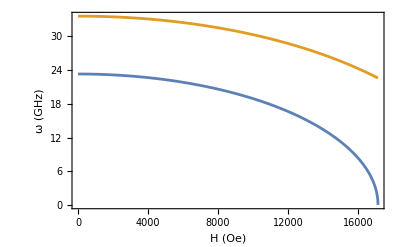

```mathematica
Clear[kx,ky,kz,J,Kx,Kz,gamma,Ms];
kx=ky=0;
kz=1;
J = 5.6*10^5;
Kx = 1.9*10^5;
Kz =1.05*10^6;
gamma=2.3*10^7;
Ms=4.2*10^2/2;
Show[Plot[{omegaLow1/(2Pi*10^9),omegaHigh1/(2Pi*10^9)},{Hz,0,2*(J+Kx+Kz)/Ms}],Frame->True,FrameLabel->{"H (Oe)","ω (GHz)"},PlotRange->All]
```

The following are parameter values for CrSBr used in the SunOrenstein paper
Kx = 2.00×10^6 J/m^3
Kz = 1.10×10^5 J/m^3
J = 6.48×10^4 J/m^3 
Ms = 2.05×10^5 A/m

```mathematica
Clear[kx,ky,kz,J,Kx,Kz,gamma,Ms];
kz=0.1;
Kx = 2*10^6;
Kz = 1.1*10^5;
J = 6.48*10^4;
gamma=2.3*10^7;
Ms=2.05*10^5;
Hz = 2*(J+Kx+Kz)/Ms;
Plot3D[omegaHigh1/(2Pi*10^9),{ky,-1,1},{kx,-1,1},AxesLabel->Automatic]
```

-Graphics3D-

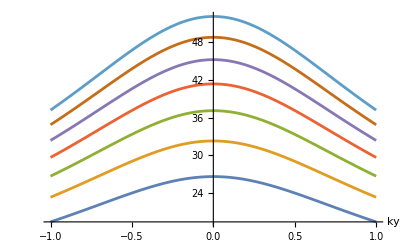

```mathematica
Clear[kx,ky,kz,J,Kx,Kz,gamma,Ms];
kz=0.1;
kx=1;
Kz = 1.1*10^5;
J = 6.48*10^4;
gamma=2.3*10^7;
Ms=2.05*10^5;
Hz=2*(J+Kx+Kz)/Ms;
T = Table[omegaHigh1/(2Pi*10^9),{Kx,1*10^6,4*10^6,0.5*10^6}];
Plot[T,{ky,-1,1},AxesLabel->Automatic]
```

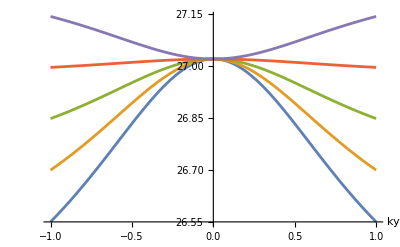

```mathematica
Clear[kx,ky,kz,J,Kx,Kz,gamma,Ms];
kz=0.1;
kx=1;
Kx = 2*10^6;
J = 6.48*10^4;
gamma=2.3*10^7;
Ms=2.05*10^5;
Hz=1.45(J+Kx+Kz)/Ms;
T = Table[omegaHigh1/(2Pi*10^9),{Kz,0.55*10^5,3*10^5,0.5*10^5}];
Plot[T,{ky,-1,1},AxesLabel->Automatic]
```

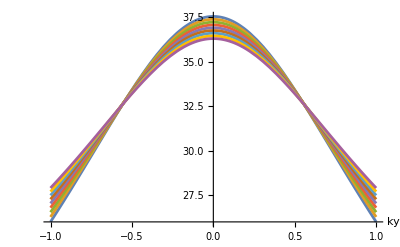

```mathematica
Clear[kx,ky,kz,J,Kx,Kz,gamma,Ms];
kz=0.1;
kx=1;
Kx = 2*10^6;
Kz = 1.1*10^5;
J = 6.48*10^4;
gamma=2.3*10^7;
Ms=2.05*10^5;
Hz=2*(J+Kx+Kz)/Ms;
T = Table[omegaHigh1/(2Pi*10^9),{J,1*10^4,18*10^4,2*10^4}];
Plot[T,{ky,-1,1},AxesLabel->Automatic]
```